## Farey Sequence and quotient distribution

```mathematica
fseq=FareySequence[100]⟦2;;⟧;
```

```mathematica
ListPlot[Table[fseq⟦i⟧,{i,1,Length[fseq]}], AspectRatio->2]
```

```mathematica
nkList={Numerator[fseq],Denominator[fseq]}//Transpose
```

{{1,100},{1,99},{1,98},{1,97},{1,96},{1,95},{1,94},{1,93},{1,92},{1,91},{1,90},{1,89},{1,88},{1,87},{1,86},{1,85},{1,84},{1,83},{1,82},{1,81},{1,80},{1,79},{1,78},{1,77},{1,76},{1,75},{1,74},{1,73},{1,72},{1,71},{1,70},{1,69},{1,68},{1,67},{1,66},{1,65},{1,64},{1,63},{1,62},2966,{62,63},{63,64},{64,65},{65,66},{66,67},{67,68},{68,69},{69,70},{70,71},{71,72},{72,73},{73,74},{74,75},{75,76},{76,77},{77,78},{78,79},{79,80},{80,81},{81,82},{82,83},{83,84},{84,85},{85,86},{86,87},{87,88},{88,89},{89,90},{90,91},{91,92},{92,93},{93,94},{94,95},{95,96},{96,97},{97,98},{98,99},{99,100},{1,1}}
 |  |  |  |

```mathematica
naturalNormals=Table[RandomVariate[NormalDistribution[i,7],10000],{i,1,100}];
quotientDist=Table[naturalNormals⟦i⟦1⟧⟧/naturalNormals⟦i⟦2⟧⟧,{i,nkList}];
quotientDist⟦3044⟧=RandomVariate[NormalDistribution[1,7],10000]/RandomVariate[NormalDistribution[1,7],10000];
```

```mathematica
skd = ParallelTable[SmoothKernelDistribution[i],{i,quotientDist}];
```

```mathematica
maxqD=Max/@quotientDist;
minqD=Min/@quotientDist;
{minqD//Min, maxqD//Max}
```

{-49991.9,62511.8}

```mathematica
discrDistr=ParallelTable[Table[PDF[i,x],{x,0,2.3,0.001}],{i,skd}];
```

## Check fitting quality

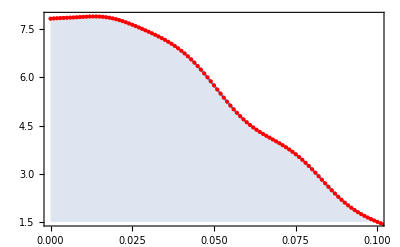

```mathematica
rys1=Plot[PDF[skd⟦1⟧,x],{x,0,0.1},PlotRange->Full,Frame->True,Filling->Axis];
rys2=ListPlot[{Table[i,{i,0,2.3,0.001}],discrDistr⟦1⟧}//Transpose,PlotRange->{{0,0.1},Automatic},PlotStyle->{Red,PointSize[Medium]}];
Show[rys1, rys2]
```

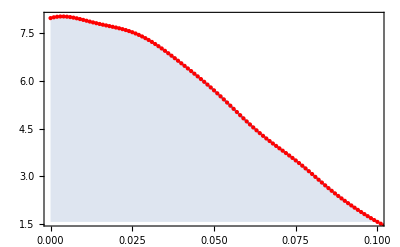

```mathematica
rys1=Plot[PDF[skd⟦2⟧,x],{x,0,0.1},PlotRange->Full,Frame->True,Filling->Axis];
rys2=ListPlot[{Table[i,{i,0,2.3,0.001}],discrDistr⟦2⟧}//Transpose,PlotRange->{{0,0.1},Automatic},PlotStyle->{Red,PointSize[Medium]}];
Show[rys1, rys2]
```

```mathematica
fint[i_,j_]:=NIntegrate[PDF[skd⟦i⟧,x]PDF[skd⟦j⟧,x],{x,0,1.2 Max[maxqD⟦i⟧,maxqD⟦j⟧]}]
dint[i_,j_]:=Dot[discrDistr⟦i⟧,discrDistr⟦j⟧]*0.001
```

```mathematica
{fint[1000,3000],dint[1000,3000]}
```

{0.000594623,0.000594632}

## Compute matrices

```mathematica
rrmatrix=ParallelArray[dint,{Length[discrDistr],Length[discrDistr]}];
```

```mathematica
rrmatrix//Flatten//Length
```

9265936

```mathematica
MatrixPlot[rrmatrix,PlotLegends->Automatic ]
```

-Graphics-

## Save results

```mathematica
SetDirectory["/Users/franciszekrakowski/cognitive/kwantyfikatory/constant_sigma"]
```

/Users/franciszekrakowski/cognitive/kwantyfikatory/constant_sigma

```mathematica
Export["quotient_elements.h5",rrmatrix]
```

quotient_elements.h5

```mathematica
Export["nklist.h5",nkList]
```

nklist.h5

```mathematica
Export["x.h5",Table[x,{x,0,2.3,0.001}]]
```

x.h5

```mathematica
discrDistr//Dimensions
```

{3044,2301}

```mathematica
Export["quotient_discrete_Ri_sigma_7.h5",discrDistr]
```

quotient_discrete_Ri_sigma_7.h5

## Numeric reactive units.

```mathematica
xList=Table[x,{x,0,150,0.01}];
ruNumeric=ParallelTable[Table[PDF[NormalDistribution[n,5],x],{x,xList}]/.x_/;x<0.0001->0,{n,1,100}];
```

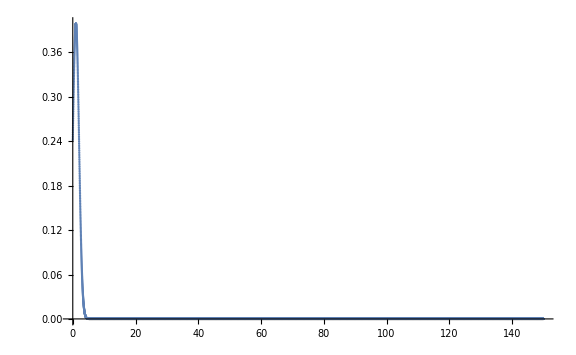

```mathematica
ListPlot[{xList,ruNumeric⟦1⟧}//Transpose,PlotRange->All,ImageSize->Large]
```

```mathematica
numDot[i_,j_]:=Dot[ruNumeric⟦i⟧,ruNumeric⟦j⟧] 0.01
numrrmatrix=ParallelArray[numDot,{Length[ruNumeric],Length[ruNumeric]}];
```

```mathematica
Export["numeric_elements.h5",numrrmatrix]
```

numeric_elements.h5

```mathematica
Export["numeric_discrete_Ri_sigma_5.h5",ruNumeric]
```

numeric_discrete_Ri_sigma_5.h5

```mathematica
rrmatrix//TableForm
```

2.82095 | 0.0000670378 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0000670378 | 1.41047 | 0.0236272 | 0.0000298289 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0236272 | 0.940316 | 0.107977 | 0.00189352 | 0.0000178628 | 2.11931×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0000298289 | 0.107977 | 0.705237 | 0.184029 | 0.0118084 | 0.000471512 | 0.0000123556 | 8.45863×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.00189352 | 0.184029 | 0.56419 | 0.225042 | 0.0310755 | 0.00268089 | 0.000188303 | 9.07619×10^-6 | 1.74204×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0000178628 | 0.0118084 | 0.225042 | 0.470158 | 0.240288 | 0.0539853 | 0.00786803 | 0.00093847 | 0.0000963849 | 7.00461×10^-6 | 2.52358×10^-7 | 1.66179×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 2.11931×10^-8 | 0.000471512 | 0.0310755 | 0.240288 | 0.402993 | 0.241104 | 0.0751226 | 0.0159386 | 0.00275371 | 0.000425512 | 0.0000567842 | 5.58521×10^-6 | 3.20041×10^-7 | 6.50962×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0000123556 | 0.00268089 | 0.0539853 | 0.241104 | 0.352618 | 0.234676 | 0.0920128 | 0.0257518 | 0.00589795 | 0.00120737 | 0.00022723 | 0.0000369404 | 4.55286×10^-6 | 3.66258×10^-7 | 1.41344×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 8.45863×10^-8 | 0.000188303 | 0.00786803 | 0.0751226 | 0.234676 | 0.313439 | 0.224957 | 0.104287 | 0.0359877 | 0.0102747 | 0.00261603 | 0.000619309 | 0.000135413 | 0.0000256459 | 3.81423×10^-6 | 4.00207×10^-7 | 2.3133×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 9.07619×10^-6 | 0.00093847 | 0.0159386 | 0.0920128 | 0.224957 | 0.282095 | 0.214021 | 0.11252 | 0.0456533 | 0.0155328 | 0.00471533 | 0.00133163 | 0.000355128 | 0.0000874721 | 0.0000187865 | 3.23336×10^-6 | 4.18449×10^-7 | 3.3684×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.74204×10^-7 | 0.0000963849 | 0.00275371 | 0.0257518 | 0.104287 | 0.214021 | 0.25645 | 0.202929 | 0.117542 | 0.0541804 | 0.0212356 | 0.00744976 | 0.00242891 | 0.0007522 | 0.00022114 | 0.0000598381 | 0.0000142495 | 2.79059×10^-6 | 4.22722×10^-7 | 4.35542×10^-8 | 6.94387×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 7.00461×10^-6 | 0.000425512 | 0.00589795 | 0.0359877 | 0.11252 | 0.202929 | 0.235079 | 0.192204 | 0.120144 | 0.0613405 | 0.0269888 | 0.010679 | 0.00392692 | 0.00137262 | 0.000459902 | 0.000146424 | 0.0000429092 | 0.0000111013 | 2.42168×10^-6 | 4.23067×10^-7 | 5.22189×10^-8 | 2.13014×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2.52358×10^-7 | 0.0000567842 | 0.00120737 | 0.0102747 | 0.0456533 | 0.117542 | 0.192204 | 0.216996 | 0.182084 | 0.120978 | 0.0671209 | 0.0324942 | 0.0142253 | 0.00579361 | 0.00224205 | 0.0008349 | 0.000299119 | 0.000101608 | 0.0000318291 | 8.88169×10^-6 | 2.10868×10^-6 | 4.14342×10^-7 | 6.13027×10^-8 | 3.86448×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.66179×10^-9 | 5.58521×10^-6 | 0.00022723 | 0.00261603 | 0.0155328 | 0.0541804 | 0.120144 | 0.182084 | 0.201496 | 0.172659 | 0.120552 | 0.0716264 | 0.0375584 | 0.0179127 | 0.0079631 | 0.00336373 | 0.00136806 | 0.000538563 | 0.000204173 | 0.000073342 | 0.0000242598 | 7.22561×10^-6 | 1.8771×10^-6 | 4.05335×10^-7 | 6.77149×10^-8 | 6.09294×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 3.20041×10^-7 | 0.0000369404 | 0.000619309 | 0.00471533 | 0.0212356 | 0.0613405 | 0.120978 | 0.172659 | 0.188063 | 0.163943 | 0.119245 | 0.0750127 | 0.0420751 | 0.0215892 | 0.0103513 | 0.00471785 | 0.0020705 | 0.00088159 | 0.000364344 | 0.000144776 | 0.0000545296 | 0.0000190451 | 5.98897×10^-6 | 1.65696×10^-6 | 3.95064×10^-7 | 7.43572×10^-8 | 8.18673×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 6.50962×10^-9 | 4.55286×10^-6 | 0.000135413 | 0.00133163 | 0.00744976 | 0.0269888 | 0.0671209 | 0.120552 | 0.163943 | 0.176309 | 0.155908 | 0.117338 | 0.0774485 | 0.0460041 | 0.0251374 | 0.0128706 | 0.00626978 | 0.0029411 | 0.0013396 | 0.000594229 | 0.000256108 | 0.000106218 | 0.0000416454 | 0.0000151545 | 5.04581×10^-6 | 1.48925×10^-6 | 3.80325×10^-7 | 7.91054×10^-8 | 1.04248×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.66258×10^-7 | 0.0000256459 | 0.000355128 | 0.00242891 | 0.010679 | 0.0324942 | 0.0716264 | 0.119245 | 0.155908 | 0.165938 | 0.14851 | 0.115033 | 0.0790947 | 0.0493495 | 0.0284739 | 0.0154398 | 0.00797527 | 0.00396787 | 0.00191707 | 0.000903932 | 0.000416123 | 0.00018594 | 0.0000798212 | 0.0000325435 | 0.0000123398 | 4.28561×10^-6 | 1.33821×10^-6 | 3.66277×10^-7 | 8.32342×10^-8 | 1.24295×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.41344×10^-8 | 3.81423×10^-6 | 0.0000874721 | 0.0007522 | 0.00392692 | 0.0142253 | 0.0375584 | 0.0750127 | 0.117338 | 0.14851 | 0.156719 | 0.141698 | 0.112478 | 0.0800952 | 0.0521421 | 0.0315461 | 0.0179895 | 0.00978678 | 0.00513051 | 0.00261242 | 0.00129913 | 0.000632174 | 0.000300442 | 0.000138734 | 0.0000615034 | 0.0000258602 | 0.000010169 | 3.6856×10^-6 | 1.21145×10^-6 | 3.49376×10^-7 | 8.56133×10^-8 | 1.44387×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.00207×10^-7 | 0.0000187865 | 0.00022114 | 0.00137262 | 0.00579361 | 0.0179127 | 0.0420751 | 0.0774485 | 0.115033 | 0.141698 | 0.148471 | 0.13542 | 0.109779 | 0.0805742 | 0.0544277 | 0.0343255 | 0.0204644 | 0.011658 | 0.00640398 | 0.00341753 | 0.00178156 | 0.000910078 | 0.00045582 | 0.000222964 | 0.000105811 | 0.0000482507 | 0.0000209039 | 8.50087×10^-6 | 3.18571×10^-6 | 1.09556×10^-6 | 3.33768×10^-7 | 8.75414×10^-8 | 1.64235×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.3133×10^-8 | 3.23336×10^-6 | 0.0000598381 | 0.000459902 | 0.00224205 | 0.0079631 | 0.0215892 | 0.0460041 | 0.0790947 | 0.112478 | 0.13542 | 0.141047 | 0.129626 | 0.107011 | 0.0806361 | 0.0562589 | 0.0368023 | 0.0228229 | 0.0135471 | 0.00776028 | 0.00431977 | 0.00234937 | 0.00125313 | 0.000656353 | 0.000337166 | 0.000169156 | 0.000082315 | 0.0000385103 | 0.0000170929 | 7.16209×10^-6 | 2.77931×10^-6 | 9.96051×10^-7 | 3.18795×10^-7 | 8.87665×10^-8 | 1.81834×10^-8 | 3.14561×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.18449×10^-7 | 0.0000142495 | 0.000146424 | 0.0008349 | 0.00336373 | 0.0103513 | 0.0251374 | 0.0493495 | 0.0800952 | 0.109779 | 0.129626 | 0.134331 | 0.124269 | 0.104227 | 0.0803675 | 0.0576892 | 0.0389799 | 0.0250366 | 0.0154182 | 0.00917188 | 0.00530407 | 0.00299752 | 0.00166175 | 0.000905665 | 0.000485294 | 0.000255089 | 0.000130922 | 0.0000650644 | 0.0000311424 | 0.0000141672 | 6.10482×10^-6 | 2.44765×10^-6 | 9.11549×10^-7 | 3.05461×10^-7 | 8.89034×10^-8 | 1.96881×10^-8 | 1.00131×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.3684×10^-8 | 2.79059×10^-6 | 0.0000429092 | 0.000299119 | 0.00136806 | 0.00471785 | 0.0128706 | 0.0284739 | 0.0521421 | 0.0805742 | 0.107011 | 0.124269 | 0.128225 | 0.119308 | 0.101464 | 0.0798394 | 0.0587701 | 0.0408701 | 0.0270872 | 0.0172419 | 0.0106124 | 0.0063532 | 0.00371748 | 0.00213428 | 0.00120536 | 0.000670294 | 0.000366699 | 0.000196628 | 0.000102967 | 0.0000522071 | 0.0000255204 | 0.0000118791 | 5.25423×10^-6 | 2.17132×10^-6 | 8.31755×10^-7 | 2.90033×10^-7 | 8.95506×10^-8 | 2.13014×10^-8 | 1.51949×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.22722×10^-7 | 0.0000111013 | 0.000101608 | 0.000538563 | 0.0020705 | 0.00626978 | 0.0154398 | 0.0315461 | 0.0544277 | 0.0806361 | 0.104227 | 0.119308 | 0.12265 | 0.114704 | 0.0987504 | 0.0791096 | 0.0595497 | 0.0424907 | 0.0289651 | 0.0189955 | 0.0120585 | 0.00744961 | 0.00449956 | 0.00266702 | 0.00155559 | 0.000894205 | 0.00050644 | 0.000282275 | 0.000154158 | 0.0000822152 | 0.0000424617 | 0.000021168 | 0.0000100677 | 4.54305×10^-6 | 1.9291×10^-6 | 7.67938×10^-7 | 2.78278×10^-7 | 8.89706×10^-8 | 2.20842×10^-8 | 1.93905×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.35542×10^-8 | 2.42168×10^-6 | 0.0000318291 | 0.000204173 | 0.00088159 | 0.0029411 | 0.00797527 | 0.0179895 | 0.0343255 | 0.0562589 | 0.0803675 | 0.101464 | 0.114704 | 0.117539 | 0.110423 | 0.0961017 | 0.078225 | 0.060071 | 0.0438622 | 0.0306677 | 0.020662 | 0.0134896 | 0.00857642 | 0.00533273 | 0.00325453 | 0.00195495 | 0.00115779 | 0.000676618 | 0.000389743 | 0.000220945 | 0.000122691 | 0.0000665381 | 0.0000349582 | 0.0000177022 | 8.58488×10^-6 | 3.97834×10^-6 | 1.73472×10^-6 | 7.07186×10^-7 | 2.62941×10^-7 | 8.73215×10^-8 | 2.3155×10^-8 | 2.50767×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.94387×10^-10 | 4.23067×10^-7 | 8.88169×10^-6 | 0.000073342 | 0.000364344 | 0.0013396 | 0.00396787 | 0.00978678 | 0.0204644 | 0.0368023 | 0.0576892 | 0.0798394 | 0.0987504 | 0.110423 | 0.112838 | 0.106434 | 0.0935299 | 0.0772235 | 0.0603726 | 0.0450065 | 0.0321969 | 0.0222299 | 0.014889 | 0.00971785 | 0.00620553 | 0.00389017 | 0.00240058 | 0.00146122 | 0.000878125 | 0.000521127 | 0.000304865 | 0.000175521 | 0.0000989635 | 0.0000544206 | 0.0000290364 | 0.0000149916 | 7.41115×10^-6 | 3.4944×10^-6 | 1.5521×10^-6 | 6.49596×10^-7 | 2.51006×10^-7 | 8.65498×10^-8 | 2.4144×10^-8 | 2.95241×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.22189×10^-8 | 2.10868×10^-6 | 0.0000242598 | 0.000144776 | 0.000594229 | 0.00191707 | 0.00513051 | 0.011658 | 0.0228229 | 0.0389799 | 0.0587701 | 0.0791096 | 0.0961017 | 0.106434 | 0.108498 | 0.102711 | 0.0910418 | 0.0761354 | 0.0604883 | 0.0459456 | 0.0335583 | 0.0236918 | 0.0162429 | 0.0108596 | 0.00710646 | 0.00456631 | 0.00288884 | 0.00180297 | 0.0011117 | 0.000677342 | 0.00040773 | 0.000241936 | 0.000141154 | 0.0000806805 | 0.00004506 | 0.0000244052 | 0.0000127711 | 6.40083×10^-6 | 3.07524×10^-6 | 1.40301×10^-6 | 6.02316×10^-7 | 2.39567×10^-7 | 8.45584×10^-8 | 2.45064×10^-8 | 3.28222×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.13014×10^-9 | 4.14342×10^-7 | 7.22561×10^-6 | 0.0000545296 | 0.000256108 | 0.000903932 | 0.00261242 | 0.00640398 | 0.0135471 | 0.0250366 | 0.0408701 | 0.0595497 | 0.078225 | 0.0935299 | 0.102711 | 0.10448 | 0.0992289 | 0.0886412 | 0.0749854 | 0.0604474 | 0.0467007 | 0.03476 | 0.025044 | 0.017541 | 0.0119896 | 0.00802486 | 0.00527556 | 0.00341506 | 0.00218144 | 0.00137689 | 0.000859542 | 0.000530517 | 0.00032344 | 0.000194402 | 0.000114978 | 0.0000665803 | 0.000037623 | 0.0000206098 | 0.0000109398 | 5.59079×10^-6 | 2.73687×10^-6 | 1.2755×10^-6 | 5.57442×10^-7 | 2.27637×10^-7 | 8.28629×10^-8 | 2.49852×10^-8 | 3.72834×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.13027×10^-8 | 1.8771×10^-6 | 0.0000190451 | 0.000106218 | 0.000416123 | 0.00129913 | 0.00341753 | 0.00776028 | 0.0154182 | 0.0270872 | 0.0424907 | 0.060071 | 0.0772235 | 0.0910418 | 0.0992289 | 0.100748 | 0.0959667 | 0.0863296 | 0.0737929 | 0.0602753 | 0.047292 | 0.0358114 | 0.0262858 | 0.0187755 | 0.0130971 | 0.00895073 | 0.00600981 | 0.00397421 | 0.00259355 | 0.00167299 | 0.00106761 | 0.000674201 | 0.000421118 | 0.00025996 | 0.000158141 | 0.0000945713 | 0.0000553346 | 0.0000316372 | 0.0000175882 | 9.46918×10^-6 | 4.91622×10^-6 | 2.43913×10^-6 | 1.15884×10^-6 | 5.17665×10^-7 | 2.16686×10^-7 | 8.11874×10^-8 | 2.50509×10^-8 | 4.17103×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.86448×10^-9 | 4.05335×10^-7 | 5.98897×10^-6 | 0.0000416454 | 0.00018594 | 0.000632174 | 0.00178156 | 0.00431977 | 0.00917188 | 0.0172419 | 0.0289651 | 0.0438622 | 0.0603726 | 0.0761354 | 0.0886412 | 0.0959667 | 0.0972741 | 0.0929048 | 0.0841067 | 0.0725737 | 0.059994 | 0.0477382 | 0.0367228 | 0.0274183 | 0.019941 | 0.0141737 | 0.00987484 | 0.00676147 | 0.00456055 | 0.00303616 | 0.00199813 | 0.00130135 | 0.000839197 | 0.000535915 | 0.000338514 | 0.000211214 | 0.00012979 | 0.0000784404 | 0.0000464534 | 0.0000268661 | 0.0000151204 | 8.22605×10^-6 | 4.33239×10^-6 | 2.18427×10^-6 | 1.05664×10^-6 | 4.81676×10^-7 | 2.04696×10^-7 | 7.9279×10^-8 | 2.52443×10^-8 | 4.33582×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.77149×10^-8 | 1.65696×10^-6 | 0.0000151545 | 0.0000798212 | 0.000300442 | 0.000910078 | 0.00234937 | 0.00530407 | 0.0106124 | 0.0189955 | 0.0306677 | 0.0450065 | 0.0604883 | 0.0749854 | 0.0863296 | 0.0929048 | 0.0940316 | 0.0900261 | 0.0819713 | 0.0713402 | 0.0596221 | 0.0480564 | 0.0375049 | 0.0284444 | 0.0210343 | 0.0152123 | 0.0107895 | 0.00752335 | 0.00516878 | 0.00350546 | 0.0023505 | 0.00156005 | 0.00102575 | 0.000668148 | 0.000431006 | 0.000274937 | 0.000173271 | 0.000107619 | 0.0000657047 | 0.0000393173 | 0.0000229421 | 0.0000130578 | 7.19157×10^-6 | 3.83972×10^-6 | 1.96572×10^-6 | 9.62377×10^-7 | 4.49475×10^-7 | 1.95139×10^-7 | 7.67017×10^-8 | 2.50537×10^-8 | 4.64255×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.09294×10^-9 | 3.95064×10^-7 | 5.04581×10^-6 | 0.0000325435 | 0.000138734 | 0.00045582 | 0.00125313 | 0.00299752 | 0.0063532 | 0.0120585 | 0.020662 | 0.0321969 | 0.0459456 | 0.0604474 | 0.0737929 | 0.0841067 | 0.0900261 | 0.0909983 | 0.0873153 | 0.0799213 | 0.0701023 | 0.0591758 | 0.0482622 | 0.0381682 | 0.0293685 | 0.0220538 | 0.016208 | 0.0116878 | 0.00828899 | 0.00579337 | 0.00399771 | 0.00272775 | 0.00184271 | 0.00123338 | 0.000818284 | 0.000537935 | 0.00035031 | 0.000225678 | 0.000143583 | 0.0000900273 | 0.0000554208 | 0.0000334799 | 0.000019731 | 0.000011352 | 6.32648×10^-6 | 3.41018×10^-6 | 1.77821×10^-6 | 8.85078×10^-7 | 4.18559×10^-7 | 1.85321×10^-7 | 7.51644×10^-8 | 2.53403×10^-8 | 4.90772×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.43572×10^-8 | 1.48925×10^-6 | 0.0000123398 | 0.0000615034 | 0.000222964 | 0.000656353 | 0.00166175 | 0.00371748 | 0.00744961 | 0.0134896 | 0.0222299 | 0.0335583 | 0.0467007 | 0.0602753 | 0.0725737 | 0.0819713 | 0.0873153 | 0.0881546 | 0.0847585 | 0.0779539 | 0.0688678 | 0.0586685 | 0.0483696 | 0.038723 | 0.0301952 | 0.0229993 | 0.0171566 | 0.0125641 | 0.00905213 | 0.00642896 | 0.00450871 | 0.0031271 | 0.00214745 | 0.00146147 | 0.000986117 | 0.000659875 | 0.000437732 | 0.000287615 | 0.000186944 | 0.000119901 | 0.0000758268 | 0.000047083 | 0.0000286999 | 0.0000170749 | 9.89998×10^-6 | 5.59421×10^-6 | 3.05346×10^-6 | 1.60762×10^-6 | 8.1206×10^-7 | 3.92641×10^-7 | 1.77194×10^-7 | 7.27701×10^-8 | 2.50924×10^-8 | 4.88954×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.18673×10^-9 | 3.80325×10^-7 | 4.28561×10^-6 | 0.0000258602 | 0.000105811 | 0.000337166 | 0.000905665 | 0.00213428 | 0.00449956 | 0.00857642 | 0.014889 | 0.0236918 | 0.03476 | 0.047292 | 0.059994 | 0.0713402 | 0.0799213 | 0.0847585 | 0.0854833 | 0.0823435 | 0.0760662 | 0.0676429 | 0.0581121 | 0.0483911 | 0.0391793 | 0.03093 | 0.0238715 | 0.0180557 | 0.0134136 | 0.0098076 | 0.0070707 | 0.0050346 | 0.00354559 | 0.00247263 | 0.00170907 | 0.00117167 | 0.00079689 | 0.000537643 | 0.000359636 | 0.000238173 | 0.000156072 | 0.000100904 | 0.0000643301 | 0.0000402718 | 0.0000247156 | 0.0000148647 | 8.7039×10^-6 | 4.95667×10^-6 | 2.73663×10^-6 | 1.46545×10^-6 | 7.5125×10^-7 | 3.67047×10^-7 | 1.68466×10^-7 | 6.9864×10^-8 | 2.45144×10^-8 | 5.01429×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.91054×10^-8 | 1.33821×10^-6 | 0.000010169 | 0.0000482507 | 0.000169156 | 0.000485294 | 0.00120536 | 0.00266702 | 0.00533273 | 0.00971785 | 0.0162429 | 0.025044 | 0.0358114 | 0.0477382 | 0.0596221 | 0.0701023 | 0.0779539 | 0.0823435 | 0.082969 | 0.080059 | 0.074255 | 0.0664323 | 0.0575163 | 0.0483379 | 0.0395463 | 0.0315785 | 0.0246723 | 0.0189034 | 0.0142328 | 0.0105508 | 0.00771406 | 0.00557134 | 0.00398031 | 0.00281616 | 0.0019752 | 0.0013743 | 0.000948934 | 0.000650297 | 0.000442044 | 0.000297982 | 0.000198852 | 0.000131299 | 0.0000855267 | 0.0000548789 | 0.0000346638 | 0.0000214478 | 0.0000129842 | 7.67192×10^-6 | 4.42643×10^-6 | 2.4722×10^-6 | 1.33514×10^-6 | 6.93668×10^-7 | 3.41948×10^-7 | 1.59298×10^-7 | 6.77052×10^-8 | 2.42437×10^-8 | 5.12987×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.04248×10^-8 | 3.66277×10^-7 | 3.6856×10^-6 | 0.0000209039 | 0.000082315 | 0.000255089 | 0.000670294 | 0.00155559 | 0.00325453 | 0.00620553 | 0.0108596 | 0.017541 | 0.0262858 | 0.0367228 | 0.0480564 | 0.0591758 | 0.0688678 | 0.0760662 | 0.080059 | 0.0805985 | 0.0778951 | 0.072517 | 0.0652396 | 0.0568895 | 0.04822 | 0.0398327 | 0.0321465 | 0.0254038 | 0.0196992 | 0.0150187 | 0.0112778 | 0.00835483 | 0.00611527 | 0.00442821 | 0.00317603 | 0.00225838 | 0.00159327 | 0.00111577 | 0.000775671 | 0.000535369 | 0.000366552 | 0.000248888 | 0.000167278 | 0.000111156 | 0.0000729749 | 0.0000471617 | 0.0000299664 | 0.0000186806 | 0.0000114257 | 6.81309×10^-6 | 3.95825×10^-6 | 2.23416×10^-6 | 1.21558×10^-6 | 6.3924×10^-7 | 3.21123×10^-7 | 1.5189×10^-7 | 6.5642×10^-8 | 2.36668×10^-8 | 5.08728×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.32342×10^-8 | 1.21145×10^-6 | 8.50087×10^-6 | 0.0000385103 | 0.000130922 | 0.000366699 | 0.000894205 | 0.00195495 | 0.00389017 | 0.00710646 | 0.0119896 | 0.0187755 | 0.0274183 | 0.0375049 | 0.0482622 | 0.0586685 | 0.0676429 | 0.074255 | 0.0778951 | 0.0783597 | 0.0758426 | 0.070849 | 0.0640677 | 0.0562389 | 0.0480462 | 0.0400467 | 0.0326398 | 0.0260689 | 0.0204431 | 0.0157693 | 0.0119853 | 0.00898936 | 0.00666284 | 0.00488647 | 0.00354992 | 0.00255707 | 0.00182767 | 0.00129686 | 0.000913926 | 0.000639549 | 0.000444415 | 0.000306348 | 0.000209327 | 0.0001417 | 0.0000947882 | 0.0000625847 | 0.0000407132 | 0.0000260873 | 0.0000163852 | 0.0000100806 | 6.06178×10^-6 | 3.54327×10^-6 | 2.01934×10^-6 | 1.11507×10^-6 | 5.9359×10^-7 | 3.02184×10^-7 | 1.44041×10^-7 | 6.31322×10^-8 | 2.33845×10^-8 | 5.03937×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.24295×10^-8 | 3.49376×10^-7 | 3.18571×10^-6 | 0.0000170929 | 0.0000650644 | 0.000196628 | 0.00050644 | 0.00115779 | 0.00240058 | 0.00456631 | 0.00802486 | 0.0130971 | 0.019941 | 0.0284444 | 0.0381682 | 0.0483696 | 0.0581121 | 0.0664323 | 0.072517 | 0.0758426 | 0.0762418 | 0.0738934 | 0.0692478 | 0.0629186 | 0.0555704 | 0.0478243 | 0.0401956 | 0.0330638 | 0.0266705 | 0.0211355 | 0.0164831 | 0.0126706 | 0.00961433 | 0.00721085 | 0.00535208 | 0.00393546 | 0.00286953 | 0.00207628 | 0.00149178 | 0.00106458 | 0.000754812 | 0.000531527 | 0.000371616 | 0.000257875 | 0.000177323 | 0.000120715 | 0.0000812423 | 0.0000540288 | 0.0000353766 | 0.000022786 | 0.0000144107 | 8.91116×10^-6 | 5.39984×10^-6 | 3.19292×10^-6 | 1.83732×10^-6 | 1.0253×10^-6 | 5.49428×10^-7 | 2.8293×10^-7 | 1.37404×10^-7 | 6.05394×10^-8 | 2.26568×10^-8 | 4.86871×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.56133×10^-8 | 1.09556×10^-6 | 7.16209×10^-6 | 0.0000311424 | 0.000102967 | 0.000282275 | 0.000676618 | 0.00146122 | 0.00288884 | 0.00527556 | 0.00895073 | 0.0141737 | 0.0210343 | 0.0293685 | 0.038723 | 0.0483911 | 0.0575163 | 0.0652396 | 0.070849 | 0.0738934 | 0.0742355 | 0.07204 | 0.06771 | 0.0617939 | 0.0548892 | 0.0475612 | 0.0402863 | 0.033424 | 0.0272119 | 0.0217775 | 0.0171593 | 0.0133316 | 0.0102271 | 0.00775645 | 0.0058225 | 0.00433056 | 0.00319413 | 0.0023382 | 0.0016997 | 0.00122758 | 0.00088094 | 0.000628173 | 0.000445075 | 0.000313052 | 0.000218458 | 0.000151096 | 0.000103532 | 0.0000700941 | 0.0000468463 | 0.0000308583 | 0.0000199672 | 0.0000127088 | 7.93138×10^-6 | 4.84408×10^-6 | 2.88904×10^-6 | 1.67213×10^-6 | 9.42251×10^-7 | 5.12732×10^-7 | 2.65779×10^-7 | 1.3064×10^-7 | 5.82947×10^-8 | 2.21034×10^-8 | 4.81353×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.44387×10^-8 | 3.33768×10^-7 | 2.77931×10^-6 | 0.0000141672 | 0.0000522071 | 0.000154158 | 0.000389743 | 0.000878125 | 0.00180297 | 0.00341506 | 0.00600981 | 0.00987484 | 0.0152123 | 0.0220538 | 0.0301952 | 0.0391793 | 0.0483379 | 0.0568895 | 0.0640677 | 0.0692478 | 0.07204 | 0.072332 | 0.0702757 | 0.0662327 | 0.0606944 | 0.0541996 | 0.0472628 | 0.040325 | 0.0337255 | 0.0276965 | 0.0223705 | 0.0177976 | 0.0139667 | 0.0108253 | 0.00829686 | 0.00629503 | 0.0047328 | 0.0035291 | 0.00261187 | 0.00191987 | 0.00140215 | 0.00101777 | 0.0007344 | 0.000526609 | 0.000375144 | 0.000265342 | 0.000186281 | 0.000129567 | 0.0000892127 | 0.0000607299 | 0.0000407646 | 0.000027 | 0.0000176013 | 0.0000112754 | 7.08584×10^-6 | 4.34848×10^-6 | 2.61379×10^-6 | 1.53122×10^-6 | 8.6768×10^-7 | 4.76819×10^-7 | 2.49753×10^-7 | 1.24085×10^-7 | 5.59591×10^-8 | 2.1406×10^-8 | 4.6385×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.75414×10^-8 | 9.96051×10^-7 | 6.10482×10^-6 | 0.0000255204 | 0.0000822152 | 0.000220945 | 0.000521127 | 0.0011117 | 0.00218144 | 0.00397421 | 0.00676147 | 0.0107895 | 0.016208 | 0.0229993 | 0.03093 | 0.0395463 | 0.04822 | 0.0562389 | 0.0629186 | 0.06771 | 0.0702757 | 0.0705237 | 0.0685944 | 0.0648129 | 0.0596209 | 0.053505 | 0.0469346 | 0.0403173 | 0.0339733 | 0.0281277 | 0.0229161 | 0.0183981 | 0.0145748 | 0.0114069 | 0.0088299 | 0.00676744 | 0.00514031 | 0.00387269 | 0.00289621 | 0.00215127 | 0.0015879 | 0.00116518 | 0.000849993 | 0.000616453 | 0.00044437 | 0.000318337 | 0.000226375 | 0.0001597 | 0.000111655 | 0.0000772135 | 0.0000528261 | 0.0000356842 | 0.0000237666 | 0.0000155846 | 0.0000100256 | 6.3412×10^-6 | 3.92964×10^-6 | 2.37358×10^-6 | 1.4021×10^-6 | 8.01703×10^-7 | 4.44851×10^-7 | 2.35439×10^-7 | 1.18259×10^-7 | 5.39467×10^-8 | 2.06272×10^-8 | 4.57902×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.64235×10^-8 | 3.18795×10^-7 | 2.44765×10^-6 | 0.0000118791 | 0.0000424617 | 0.000122691 | 0.000304865 | 0.000677342 | 0.00137689 | 0.00259355 | 0.00456055 | 0.00752335 | 0.0116878 | 0.0171566 | 0.0238715 | 0.0315785 | 0.0398327 | 0.0480462 | 0.0555704 | 0.0617939 | 0.0662327 | 0.0685944 | 0.0688036 | 0.0669903 | 0.0634478 | 0.0585737 | 0.0528087 | 0.0465813 | 0.0402685 | 0.0341718 | 0.0285088 | 0.0234162 | 0.018961 | 0.0151549 | 0.0119702 | 0.00935335 | 0.00723751 | 0.00555084 | 0.00422317 | 0.00318959 | 0.00239288 | 0.00178415 | 0.0013225 | 0.000974811 | 0.000714538 | 0.000520878 | 0.000377382 | 0.000271645 | 0.000194135 | 0.000137553 | 0.0000966291 | 0.0000671958 | 0.0000462015 | 0.0000313692 | 0.0000209721 | 0.0000138264 | 8.96441×10^-6 | 5.69334×10^-6 | 3.55197×10^-6 | 2.16113×10^-6 | 1.2867×10^-6 | 7.41982×10^-7 | 4.15436×10^-7 | 2.21963×10^-7 | 1.11844×10^-7 | 5.18377×10^-8 | 1.99704×10^-8 | 4.26625×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.87665×10^-8 | 9.11549×10^-7 | 5.25423×10^-6 | 0.000021168 | 0.0000665381 | 0.000175521 | 0.00040773 | 0.000859542 | 0.00167299 | 0.00303616 | 0.00516878 | 0.00828899 | 0.0125641 | 0.0180557 | 0.0246723 | 0.0321465 | 0.0400467 | 0.0478243 | 0.0548892 | 0.0606944 | 0.0648129 | 0.0669903 | 0.0671654 | 0.0654585 | 0.0621346 | 0.057553 | 0.052113 | 0.0462068 | 0.0401831 | 0.0343254 | 0.0288431 | 0.0238728 | 0.0194871 | 0.0157068 | 0.012514 | 0.00986565 | 0.00770338 | 0.00596274 | 0.00457888 | 0.00349083 | 0.00264382 | 0.00199008 | 0.00148945 | 0.00110868 | 0.000820944 | 0.000604572 | 0.000442746 | 0.000322305 | 0.000233017 | 0.000167297 | 0.000119145 | 0.0000840888 | 0.0000587504 | 0.0000405428 | 0.0000276576 | 0.0000186112 | 0.000012315 | 8.02954×10^-6 | 5.13057×10^-6 | 3.22202×10^-6 | 1.97443×10^-6 | 1.18466×10^-6 | 6.88865×10^-7 | 3.87352×10^-7 | 2.09904×10^-7 | 1.06831×10^-7 | 4.96196×10^-8 | 1.92437×10^-8 | 4.07327×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.81834×10^-8 | 3.05461×10^-7 | 2.17132×10^-6 | 0.0000100677 | 0.0000349582 | 0.0000989635 | 0.000241936 | 0.000530517 | 0.00106761 | 0.00199813 | 0.00350546 | 0.00579337 | 0.00905213 | 0.0134136 | 0.0189034 | 0.0254038 | 0.0326398 | 0.0401956 | 0.0475612 | 0.0541996 | 0.0596209 | 0.0634478 | 0.0654585 | 0.0656034 | 0.0639941 | 0.0608708 | 0.0565585 | 0.0514202 | 0.0458149 | 0.0400654 | 0.034438 | 0.0291337 | 0.0242879 | 0.0199773 | 0.01623 | 0.0130374 | 0.0103651 | 0.00816324 | 0.00637404 | 0.00493813 | 0.00379848 | 0.00290274 | 0.00220487 | 0.00166538 | 0.00125128 | 0.00093526 | 0.000695472 | 0.000514451 | 0.000378356 | 0.000276655 | 0.00020097 | 0.000144932 | 0.000103675 | 0.0000734363 | 0.0000515293 | 0.0000357564 | 0.000024475 | 0.0000165483 | 0.0000110052 | 7.2146×10^-6 | 4.6368×10^-6 | 2.93038×10^-6 | 1.80799×10^-6 | 1.08888×10^-6 | 6.40429×10^-7 | 3.63113×10^-7 | 1.97411×10^-7 | 1.01247×10^-7 | 4.73357×10^-8 | 1.83981×10^-8 | 3.90225×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.14561×10^-10 | 8.89034×10^-8 | 8.31755×10^-7 | 4.54305×10^-6 | 0.0000177022 | 0.0000544206 | 0.000141154 | 0.00032344 | 0.000674201 | 0.00130135 | 0.0023505 | 0.00399771 | 0.00642896 | 0.0098076 | 0.0142328 | 0.0196992 | 0.0260689 | 0.0330638 | 0.0402863 | 0.0472628 | 0.053505 | 0.0585737 | 0.0621346 | 0.0639941 | 0.0641124 | 0.0625929 | 0.0596539 | 0.0555901 | 0.0507321 | 0.0454087 | 0.0399191 | 0.0345133 | 0.0293837 | 0.0246636 | 0.0204325 | 0.0167249 | 0.0135396 | 0.0108507 | 0.00861559 | 0.00678325 | 0.00529952 | 0.00411115 | 0.00316868 | 0.00242772 | 0.00184981 | 0.00140208 | 0.0010574 | 0.00079353 | 0.000592455 | 0.000440094 | 0.000325117 | 0.000238747 | 0.000174171 | 0.000126066 | 0.0000905491 | 0.0000644528 | 0.0000453743 | 0.000031619 | 0.0000217374 | 0.0000147656 | 9.86779×10^-6 | 6.50318×10^-6 | 4.2033×10^-6 | 2.66526×10^-6 | 1.65992×10^-6 | 1.00681×10^-6 | 5.94235×10^-7 | 3.39417×10^-7 | 1.85918×10^-7 | 9.60466×10^-8 | 4.55507×10^-8 | 1.7806×10^-8 | 3.60413×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.96881×10^-8 | 2.90033×10^-7 | 1.9291×10^-6 | 8.58488×10^-6 | 0.0000290364 | 0.0000806805 | 0.000194402 | 0.000421118 | 0.000839197 | 0.00156005 | 0.00272775 | 0.00450871 | 0.0070707 | 0.0105508 | 0.0150187 | 0.0204431 | 0.0266705 | 0.033424 | 0.040325 | 0.0469346 | 0.0528087 | 0.057553 | 0.0608708 | 0.0625929 | 0.0626877 | 0.061251 | 0.0584816 | 0.0546475 | 0.0500499 | 0.044991 | 0.0397477 | 0.0345549 | 0.0295961 | 0.025002 | 0.020854 | 0.0171915 | 0.0140202 | 0.0113212 | 0.00905912 | 0.00718894 | 0.00566152 | 0.00442762 | 0.00344053 | 0.00265783 | 0.00204195 | 0.00156074 | 0.0011871 | 0.000898528 | 0.000676916 | 0.000507477 | 0.000378505 | 0.000280762 | 0.000206935 | 0.00015156 | 0.000110192 | 0.0000794072 | 0.0000567433 | 0.0000401041 | 0.0000280609 | 0.000019373 | 0.0000132188 | 8.87624×10^-6 | 5.86689×10^-6 | 3.82136×10^-6 | 2.4375×10^-6 | 1.52298×10^-6 | 9.29706×10^-7 | 5.52469×10^-7 | 3.17798×10^-7 | 1.76258×10^-7 | 9.17801×10^-8 | 4.34915×10^-8 | 1.70158×10^-8 | 3.18738×10^-9 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.00131×10^-9 | 8.95506×10^-8 | 7.67938×10^-7 | 3.97834×10^-6 | 0.0000149916 | 0.00004506 | 0.000114978 | 0.00025996 | 0.000535915 | 0.00102575 | 0.00184271 | 0.0031271 | 0.0050346 | 0.00771406 | 0.0112778 | 0.0157693 | 0.0211355 | 0.0272119 | 0.0337255 | 0.0403173 | 0.0465813 | 0.052113 | 0.0565585 | 0.0596539 | 0.061251 | 0.0613249 | 0.0599648 | 0.0573518 | 0.0537301 | 0.049375 | 0.0445641 | 0.0395543 | 0.0345658 | 0.0297736 | 0.0253052 | 0.0212431 | 0.0176305 | 0.014479 | 0.0117761 | 0.00949278 | 0.00758982 | 0.00602293 | 0.0047467 | 0.00371734 | 0.00289424 | 0.00224124 | 0.0017268 | 0.001324 | 0.0010105 | 0.000767702 | 0.000580547 | 0.000436913 | 0.00032706 | 0.000243531 | 0.000180245 | 0.000132452 | 0.000096659 | 0.0000699124 | 0.0000501467 | 0.0000355769 | 0.0000249924 | 0.0000173259 | 0.0000118538 | 8.0107×10^-6 | 5.32147×10^-6 | 3.47627×10^-6 | 2.22967×10^-6 | 1.40143×10^-6 | 8.60968×10^-7 | 5.17152×10^-7 | 2.99766×10^-7 | 1.66713×10^-7 | 8.74476×10^-8 | 4.13779×10^-8 | 1.61885×10^-8 | 3.01562×10^-9 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.13014×10^-8 | 2.78278×10^-7 | 1.73472×10^-6 | 7.41115×10^-6 | 0.0000244052 | 0.0000665803 | 0.000158141 | 0.000338514 | 0.000668148 | 0.00123338 | 0.00214745 | 0.00354559 | 0.00557134 | 0.00835483 | 0.0119853 | 0.0164831 | 0.0217775 | 0.0276965 | 0.0339733 | 0.0402685 | 0.0462068 | 0.0514202 | 0.0555901 | 0.0584816 | 0.0599648 | 0.0600202 | 0.0587308 | 0.0562623 | 0.0528376 | 0.0487084 | 0.0441302 | 0.0393415 | 0.0345489 | 0.0299189 | 0.0255753 | 0.0216009 | 0.0180423 | 0.0149157 | 0.0122145 | 0.00991544 | 0.00798461 | 0.00638239 | 0.00506714 | 0.00399782 | 0.00313601 | 0.00244686 | 0.00189958 | 0.0014678 | 0.00112904 | 0.000864631 | 0.000659214 | 0.00050024 | 0.000377848 | 0.000283952 | 0.000212139 | 0.000157575 | 0.000116203 | 0.0000851022 | 0.0000617706 | 0.0000444668 | 0.000031663 | 0.0000222989 | 0.000015541 | 0.0000106778 | 7.23446×10^-6 | 4.82793×10^-6 | 3.16945×10^-6 | 2.04367×10^-6 | 1.29589×10^-6 | 8.0122×10^-7 | 4.82586×10^-7 | 2.8155×10^-7 | 1.56773×10^-7 | 8.26461×10^-8 | 3.95408×10^-8 | 1.54619×10^-8 | 2.74021×10^-9 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.51949×10^-9 | 8.89706×10^-8 | 7.07186×10^-7 | 3.4944×10^-6 | 0.0000127711 | 0.000037623 | 0.0000945713 | 0.000211214 | 0.000431006 | 0.000818284 | 0.00146147 | 0.00247263 | 0.00398031 | 0.00611527 | 0.00898936 | 0.0126706 | 0.0171593 | 0.0223705 | 0.0281277 | 0.0341718 | 0.0401831 | 0.0458149 | 0.0507321 | 0.0546475 | 0.0573518 | 0.0587308 | 0.0587697 | 0.057546 | 0.0552112 | 0.0519692 | 0.0480507 | 0.0436912 | 0.039112 | 0.034507 | 0.0300344 | 0.0258142 | 0.021929 | 0.0184276 | 0.0153305 | 0.0126361 | 0.0103264 | 0.00837238 | 0.00673889 | 0.00538782 | 0.00428108 | 0.00338233 | 0.00265811 | 0.0020787 | 0.00161806 | 0.00125393 | 0.000967577 | 0.000743359 | 0.000568683 | 0.000433109 | 0.000328219 | 0.000247514 | 0.000185549 | 0.000138297 | 0.00010233 | 0.0000751966 | 0.0000547656 | 0.0000395218 | 0.0000282702 | 0.0000199831 | 0.00001396 | 9.62913×10^-6 | 6.55129×10^-6 | 4.39163×10^-6 | 2.90423×10^-6 | 1.88286×10^-6 | 1.19709×10^-6 | 7.4443×10^-7 | 4.49313×10^-7 | 2.63626×10^-7 | 1.48374×10^-7 | 7.86687×10^-8 | 3.77987×10^-8 | 1.47632×10^-8 | 2.3548×10^-9
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.20842×10^-8 | 2.62941×10^-7 | 1.5521×10^-6 | 6.40083×10^-6 | 0.0000206098 | 0.0000553346 | 0.00012979 | 0.000274937 | 0.000537935 | 0.000986117 | 0.00170907 | 0.00281616 | 0.00442821 | 0.00666284 | 0.00961433 | 0.0133316 | 0.0177976 | 0.0229161 | 0.0285088 | 0.0343254 | 0.0400654 | 0.0454087 | 0.0500499 | 0.0537301 | 0.0562623 | 0.057546 | 0.0575704 | 0.0564075 | 0.0541967 | 0.0511244 | 0.0474027 | 0.0432486 | 0.0388679 | 0.0344424 | 0.0301225 | 0.026024 | 0.0222287 | 0.0187872 | 0.0157236 | 0.0130406 | 0.0107249 | 0.00875218 | 0.00709129 | 0.00570771 | 0.0045661 | 0.00363223 | 0.00287431 | 0.00226347 | 0.00177431 | 0.00138482 | 0.00107623 | 0.000833009 | 0.000642093 | 0.00049276 | 0.000376531 | 0.000286283 | 0.000216604 | 0.000162906 | 0.000121815 | 0.0000904235 | 0.0000666132 | 0.0000487085 | 0.0000352674 | 0.0000252837 | 0.0000179329 | 0.0000125725 | 8.70497×10^-6 | 5.95852×10^-6 | 4.01252×10^-6 | 2.65975×10^-6 | 1.73282×10^-6 | 1.10394×10^-6 | 6.89977×10^-7 | 4.20262×10^-7 | 2.47967×10^-7 | 1.40308×10^-7 | 7.47254×10^-8 | 3.56739×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.93905×10^-9 | 8.73215×10^-8 | 6.49596×10^-7 | 3.07524×10^-6 | 0.0000109398 | 0.0000316372 | 0.0000784404 | 0.000173271 | 0.00035031 | 0.000659875 | 0.00117167 | 0.0019752 | 0.00317603 | 0.00488647 | 0.00721085 | 0.0102271 | 0.0139667 | 0.0183981 | 0.0234162 | 0.0288431 | 0.034438 | 0.0399191 | 0.044991 | 0.049375 | 0.0528376 | 0.0552112 | 0.0564075 | 0.0564189 | 0.0553127 | 0.053217 | 0.0503027 | 0.0467648 | 0.0428039 | 0.0386113 | 0.0343575 | 0.0301853 | 0.0262064 | 0.0225013 | 0.019122 | 0.0160954 | 0.0134279 | 0.0111106 | 0.00912334 | 0.00743886 | 0.00602597 | 0.00485205 | 0.0038851 | 0.0030948 | 0.0024534 | 0.00193616 | 0.00152138 | 0.0011906 | 0.000928011 | 0.000720388 | 0.000557008 | 0.000428806 | 0.000328704 | 0.000250708 | 0.000190287 | 0.000143558 | 0.000107623 | 0.0000801793 | 0.0000592497 | 0.000043422 | 0.0000315364 | 0.000022681 | 0.0000161404 | 0.000011374 | 7.90616×10^-6 | 5.42355×10^-6 | 3.66782×10^-6 | 2.43613×10^-6 | 1.59438×10^-6 | 1.02386×10^-6 | 6.43391×10^-7 | 3.94089×10^-7 | 2.33853×10^-7 | 1.32365×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.3155×10^-8 | 2.51006×10^-7 | 1.40301×10^-6 | 5.59079×10^-6 | 0.0000175882 | 0.0000464534 | 0.000107619 | 0.000225678 | 0.000437732 | 0.00079689 | 0.0013743 | 0.00225838 | 0.00354992 | 0.00535208 | 0.00775645 | 0.0108253 | 0.0145748 | 0.018961 | 0.0238728 | 0.0291337 | 0.0345133 | 0.0397477 | 0.0445641 | 0.0487084 | 0.0519692 | 0.0541967 | 0.0553127 | 0.0553127 | 0.0542593 | 0.0522704 | 0.0495033 | 0.0461374 | 0.0423583 | 0.0383439 | 0.0342543 | 0.0302249 | 0.0263632 | 0.0227483 | 0.0194329 | 0.0164461 | 0.0137979 | 0.011483 | 0.00948517 | 0.00778073 | 0.00634165 | 0.00513807 | 0.00414003 | 0.00331882 | 0.00264784 | 0.00210305 | 0.00166336 | 0.0013103 | 0.00102809 | 0.000803608 | 0.000625637 | 0.000485198 | 0.000374651 | 0.000288066 | 0.000220374 | 0.000167701 | 0.000126945 | 0.0000954499 | 0.0000712736 | 0.0000528195 | 0.0000388221 | 0.0000282798 | 0.0000204278 | 0.0000145868 | 0.0000102998 | 7.18561×10^-6 | 4.93825×10^-6 | 3.35271×10^-6 | 2.24183×10^-6 | 1.47414×10^-6 | 9.51366×10^-7 | 6.00964×10^-7 | 3.68632×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.50767×10^-9 | 8.65498×10^-8 | 6.02316×10^-7 | 2.73687×10^-6 | 9.46918×10^-6 | 0.0000268661 | 0.0000657047 | 0.000143583 | 0.000287615 | 0.000537643 | 0.000948934 | 0.00159327 | 0.00255707 | 0.00393546 | 0.0058225 | 0.00829686 | 0.0114069 | 0.0151549 | 0.0194871 | 0.0242879 | 0.0293837 | 0.0345549 | 0.0395543 | 0.0441302 | 0.0480507 | 0.0511244 | 0.053217 | 0.0542593 | 0.054249 | 0.0532448 | 0.0513554 | 0.0487256 | 0.0455207 | 0.0419127 | 0.0380673 | 0.0341347 | 0.0302432 | 0.0264962 | 0.022971 | 0.0197207 | 0.0167764 | 0.0141507 | 0.0118419 | 0.00983713 | 0.00811617 | 0.00665402 | 0.00542333 | 0.00439624 | 0.00354567 | 0.00284616 | 0.00227461 | 0.0018103 | 0.001435 | 0.00113321 | 0.000891479 | 0.000698747 | 0.000545539 | 0.000424303 | 0.000328578 | 0.000253305 | 0.000194395 | 0.000148354 | 0.000112564 | 0.0000848684 | 0.0000635457 | 0.0000472226 | 0.0000348406 | 0.000025457 | 0.0000184239 | 0.0000131976 | 9.3346×10^-6 | 6.53415×10^-6 | 4.51593×10^-6 | 3.07842×10^-6 | 2.06732×10^-6 | 1.36562×10^-6 | 8.82806×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.4144×10^-8 | 2.39567×10^-7 | 1.2755×10^-6 | 4.91622×10^-6 | 0.0000151204 | 0.0000393173 | 0.0000900273 | 0.000186944 | 0.000359636 | 0.000650297 | 0.00111577 | 0.00182767 | 0.00286953 | 0.00433056 | 0.00629503 | 0.0088299 | 0.0119702 | 0.0157068 | 0.0199773 | 0.0246636 | 0.0295961 | 0.0345658 | 0.0393415 | 0.0436912 | 0.0474027 | 0.0503027 | 0.0522704 | 0.0532448 | 0.0532254 | 0.0522672 | 0.0504705 | 0.0479689 | 0.0449151 | 0.0414683 | 0.037783 | 0.0340004 | 0.030242 | 0.0266069 | 0.0231708 | 0.0199865 | 0.0170866 | 0.0144864 | 0.012187 | 0.0101788 | 0.00844463 | 0.00696235 | 0.00570709 | 0.00465303 | 0.00377465 | 0.00304786 | 0.00245029 | 0.00196174 | 0.00156452 | 0.00124301 | 0.000984009 | 0.000776104 | 0.000609952 | 0.000477515 | 0.000372357 | 0.000289209 | 0.000223572 | 0.000171988 | 0.000131603 | 0.000100117 | 0.000075682 | 0.0000568599 | 0.0000423723 | 0.0000313208 | 0.0000229498 | 0.0000166362 | 0.0000119519 | 8.4938×10^-6 | 5.96634×10^-6 | 4.13883×10^-6 | 2.83253×10^-6 | 1.9053×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.95241×10^-9 | 8.45584×10^-8 | 5.57442×10^-7 | 2.43913×10^-6 | 8.22605×10^-6 | 0.0000229421 | 0.0000554208 | 0.000119901 | 0.000238173 | 0.000442044 | 0.000775671 | 0.00129686 | 0.00207628 | 0.00319413 | 0.0047328 | 0.00676744 | 0.00935335 | 0.012514 | 0.01623 | 0.0204325 | 0.025002 | 0.0297736 | 0.0345489 | 0.039112 | 0.0432486 | 0.0467648 | 0.0495033 | 0.0513554 | 0.0522672 | 0.0522398 | 0.0513245 | 0.0496144 | 0.0472326 | 0.0443205 | 0.0410256 | 0.0374923 | 0.0338529 | 0.0302228 | 0.0266969 | 0.0233487 | 0.020231 | 0.0173774 | 0.0148052 | 0.0125182 | 0.0105098 | 0.0087655 | 0.00726595 | 0.0059886 | 0.00490961 | 0.00400516 | 0.00325227 | 0.00262948 | 0.00211736 | 0.00169838 | 0.00135734 | 0.00108085 | 0.00085772 | 0.000678204 | 0.000534327 | 0.000419471 | 0.000327963 | 0.000255341 | 0.0001979 | 0.000152629 | 0.000117085 | 0.0000893479 | 0.0000677181 | 0.0000509724 | 0.0000380827 | 0.0000281947 | 0.0000207127 | 0.0000150751 | 0.0000108629 | 7.74448×10^-6 | 5.45836×10^-6 | 3.79203×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.45064×10^-8 | 2.27637×10^-7 | 1.15884×10^-6 | 4.33239×10^-6 | 0.0000130578 | 0.0000334799 | 0.0000758268 | 0.000156072 | 0.000297982 | 0.000535369 | 0.000913926 | 0.00149178 | 0.0023382 | 0.0035291 | 0.00514031 | 0.00723751 | 0.00986565 | 0.0130374 | 0.0167249 | 0.020854 | 0.0253052 | 0.0299189 | 0.034507 | 0.0388679 | 0.0428039 | 0.0461374 | 0.0487256 | 0.0504705 | 0.0513245 | 0.0512899 | 0.050415 | 0.0487858 | 0.0465161 | 0.043737 | 0.0405855 | 0.0371963 | 0.0336939 | 0.0301873 | 0.0267677 | 0.0235063 | 0.0204554 | 0.0176494 | 0.0151075 | 0.0128357 | 0.0108299 | 0.00907845 | 0.00756436 | 0.00626733 | 0.00516552 | 0.00423663 | 0.0034589 | 0.00281191 | 0.00227673 | 0.00183645 | 0.0014759 | 0.00118203 | 0.000943392 | 0.000750357 | 0.000594829 | 0.000469819 | 0.000369703 | 0.000289777 | 0.000226174 | 0.000175728 | 0.00013592 | 0.000104529 | 0.0000799215 | 0.0000607211 | 0.0000457806 | 0.0000342854 | 0.0000254724 | 0.0000187631 | 0.0000136946 | 9.89746×10^-6 | 7.06618×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.28222×10^-9 | 8.28629×10^-8 | 5.17665×10^-7 | 2.18427×10^-6 | 7.19157×10^-6 | 0.000019731 | 0.000047083 | 0.000100904 | 0.000198852 | 0.000366552 | 0.000639549 | 0.00106458 | 0.0016997 | 0.00261187 | 0.00387269 | 0.00555084 | 0.00770338 | 0.0103651 | 0.0135396 | 0.0171915 | 0.0212431 | 0.0255753 | 0.0300344 | 0.0344424 | 0.0386113 | 0.0423583 | 0.0455207 | 0.0479689 | 0.0496144 | 0.050415 | 0.0503741 | 0.0495369 | 0.0479833 | 0.0458188 | 0.0431647 | 0.0401485 | 0.0368961 | 0.0335244 | 0.0301369 | 0.0268205 | 0.0236445 | 0.0206604 | 0.0179033 | 0.0153935 | 0.0131393 | 0.0111389 | 0.00938302 | 0.00785696 | 0.00654266 | 0.00542004 | 0.00446835 | 0.00366717 | 0.0029969 | 0.00243944 | 0.00197819 | 0.00159847 | 0.00128715 | 0.00103299 | 0.000826331 | 0.000658777 | 0.000523415 | 0.000414403 | 0.00032688 | 0.000256827 | 0.000200997 | 0.000156546 | 0.000121323 | 0.0000935214 | 0.0000716258 | 0.0000545402 | 0.0000412473 | 0.0000309655 | 0.0000230635 | 0.000017033 | 0.0000124484
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.49852×10^-8 | 2.16686×10^-7 | 1.05664×10^-6 | 3.83972×10^-6 | 0.000011352 | 0.0000286999 | 0.0000643301 | 0.000131299 | 0.000248888 | 0.000444415 | 0.000754812 | 0.00122758 | 0.00191987 | 0.00289621 | 0.00422317 | 0.00596274 | 0.00816324 | 0.0108507 | 0.0140202 | 0.0176305 | 0.0216009 | 0.0258142 | 0.0301225 | 0.0343575 | 0.0383439 | 0.0419127 | 0.0449151 | 0.0472326 | 0.0487858 | 0.0495369 | 0.0494903 | 0.0486886 | 0.0472058 | 0.0451399 | 0.0426034 | 0.0397151 | 0.0365926 | 0.0333458 | 0.0300728 | 0.0268568 | 0.0237647 | 0.0208472 | 0.0181397 | 0.0156638 | 0.0134294 | 0.0114368 | 0.00967898 | 0.00814348 | 0.00681415 | 0.0056727 | 0.00469995 | 0.0038766 | 0.00318415 | 0.00260508 | 0.00212345 | 0.00172472 | 0.00139612 | 0.00112648 | 0.000905939 | 0.000726234 | 0.000580279 | 0.000462103 | 0.000366706 | 0.000289993 | 0.000228382 | 0.000179099 | 0.000139807 | 0.000108542 | 0.0000838504 | 0.0000643987 | 0.0000491486 | 0.0000372559 | 0.0000280355 | 0.000020909
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.72834×10^-9 | 8.11874×10^-8 | 4.81676×10^-7 | 1.96572×10^-6 | 6.32648×10^-6 | 0.0000170749 | 0.0000402718 | 0.0000855267 | 0.000167278 | 0.000306348 | 0.000531527 | 0.00088094 | 0.00140215 | 0.00215127 | 0.00318959 | 0.00457888 | 0.00637404 | 0.00861559 | 0.0113212 | 0.014479 | 0.0180423 | 0.021929 | 0.026024 | 0.0301853 | 0.0342543 | 0.0380673 | 0.0414683 | 0.0443205 | 0.0465161 | 0.0479833 | 0.0486886 | 0.048637 | 0.0478686 | 0.0464523 | 0.044479 | 0.0420532 | 0.0392858 | 0.0362865 | 0.0331591 | 0.0299963 | 0.0268776 | 0.0238677 | 0.0210164 | 0.0183592 | 0.0159185 | 0.0137058 | 0.0117234 | 0.00996605 | 0.00842342 | 0.00708123 | 0.00592294 | 0.00493074 | 0.00408666 | 0.00337304 | 0.00277324 | 0.00227169 | 0.00185436 | 0.00150871 | 0.00122349 | 0.000989067 | 0.000797064 | 0.000640316 | 0.000512744 | 0.000409292 | 0.000325531 | 0.000257955 | 0.000203599 | 0.000159955 | 0.000125126 | 0.0000973941 | 0.0000754006 | 0.0000580347 | 0.0000443889 | 0.0000336928
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.50509×10^-8 | 2.04696×10^-7 | 9.62377×10^-7 | 3.41018×10^-6 | 9.89998×10^-6 | 0.0000247156 | 0.0000548789 | 0.000111156 | 0.000209327 | 0.000371616 | 0.000628173 | 0.00101777 | 0.0015879 | 0.00239288 | 0.00349083 | 0.00493813 | 0.00678325 | 0.00905912 | 0.0117761 | 0.0149157 | 0.0184276 | 0.0222287 | 0.0262064 | 0.0302249 | 0.0341347 | 0.037783 | 0.0410256 | 0.043737 | 0.0458188 | 0.0472058 | 0.0478686 | 0.0478127 | 0.0470756 | 0.0457217 | 0.0438354 | 0.041514 | 0.0388608 | 0.0359787 | 0.0329653 | 0.0299085 | 0.0268842 | 0.0239548 | 0.0211691 | 0.0185625 | 0.0161582 | 0.013969 | 0.0119987 | 0.0102441 | 0.00869652 | 0.00734359 | 0.00617031 | 0.00516036 | 0.00429687 | 0.00356325 | 0.00294347 | 0.00242266 | 0.00198718 | 0.00162459 | 0.00132394 | 0.00107561 | 0.000871202 | 0.000703494 | 0.000566388 | 0.000454516 | 0.000363538 | 0.000289759 | 0.000230036 | 0.000181937 | 0.000143281 | 0.000112317 | 0.0000876055 | 0.0000679638 | 0.000052383
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.17103×10^-9 | 7.9279×10^-8 | 4.49475×10^-7 | 1.77821×10^-6 | 5.59421×10^-6 | 0.0000148647 | 0.0000346638 | 0.0000729749 | 0.0001417 | 0.000257875 | 0.000445075 | 0.0007344 | 0.00116518 | 0.00178415 | 0.00264382 | 0.00379848 | 0.00529952 | 0.00718894 | 0.00949278 | 0.0122145 | 0.0153305 | 0.0187872 | 0.0225013 | 0.0263632 | 0.0302432 | 0.0340004 | 0.0374923 | 0.0405855 | 0.0431647 | 0.0451399 | 0.0464523 | 0.0470756 | 0.0470158 | 0.0463083 | 0.045013 | 0.0432086 | 0.0409856 | 0.0384405 | 0.0356698 | 0.0327653 | 0.0298104 | 0.0268775 | 0.0240269 | 0.0213062 | 0.0187504 | 0.0163834 | 0.0142192 | 0.0122629 | 0.010513 | 0.00896258 | 0.00760089 | 0.00641449 | 0.00538836 | 0.00450689 | 0.00375432 | 0.00311549 | 0.00257611 | 0.00212282 | 0.00174362 | 0.00142768 | 0.00116546 | 0.000948573 | 0.000769837 | 0.000622884 | 0.000502456 | 0.000404039 | 0.000323767 | 0.00025858 | 0.000205751 | 0.000163062 | 0.000128676 | 0.000101072 | 0.000078949
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.52443×10^-8 | 1.95139×10^-7 | 8.85078×10^-7 | 3.05346×10^-6 | 8.7039×10^-6 | 0.0000214478 | 0.0000471617 | 0.0000947882 | 0.000177323 | 0.000313052 | 0.000526609 | 0.000849993 | 0.0013225 | 0.00199008 | 0.00290274 | 0.00411115 | 0.00566152 | 0.00758982 | 0.00991544 | 0.0126361 | 0.0157236 | 0.019122 | 0.0227483 | 0.0264962 | 0.030242 | 0.0338529 | 0.0371963 | 0.0401485 | 0.0426034 | 0.044479 | 0.0457217 | 0.0463083 | 0.046245 | 0.0455654 | 0.0443253 | 0.0425979 | 0.0404678 | 0.0380251 | 0.0353603 | 0.03256 | 0.029703 | 0.0268587 | 0.024085 | 0.0214283 | 0.0189233 | 0.0165945 | 0.0144565 | 0.0125159 | 0.0107726 | 0.00922129 | 0.00785276 | 0.00665497 | 0.00561429 | 0.00471614 | 0.00394579 | 0.00328885 | 0.0027315 | 0.00226096 | 0.00186547 | 0.00153443 | 0.00125838 | 0.00102906 | 0.000839073 | 0.0006822 | 0.00055304 | 0.000446925 | 0.000360084 | 0.000289164 | 0.000231401 | 0.000184487 | 0.000146496 | 0.000115777
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.33582×10^-9 | 7.67017×10^-8 | 4.18559×10^-7 | 1.60762×10^-6 | 4.95667×10^-6 | 0.0000129842 | 0.0000299664 | 0.0000625847 | 0.000120715 | 0.000218458 | 0.000375144 | 0.000616453 | 0.000974811 | 0.00148945 | 0.00220487 | 0.00316868 | 0.00442762 | 0.00602293 | 0.00798461 | 0.0103264 | 0.0130406 | 0.0160954 | 0.0194329 | 0.022971 | 0.0266069 | 0.0302228 | 0.0336939 | 0.0368961 | 0.0397151 | 0.0420532 | 0.0438354 | 0.045013 | 0.0455654 | 0.0454991 | 0.0448458 | 0.0436576 | 0.0420029 | 0.0399605 | 0.0376149 | 0.0350509 | 0.03235 | 0.0295873 | 0.0268286 | 0.0241299 | 0.0215363 | 0.0190821 | 0.016792 | 0.0146813 | 0.0127579 | 0.0110229 | 0.00947256 | 0.00809894 | 0.0068915 | 0.00583777 | 0.00492432 | 0.00413735 | 0.00346316 | 0.00288861 | 0.00240134 | 0.00198994 | 0.00164401 | 0.0013543 | 0.00111243 | 0.000911206 | 0.000744298 | 0.00060619 | 0.000492329 | 0.000398665 | 0.000321816 | 0.000258926 | 0.000207598 | 0.000165767
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.50537×10^-8 | 1.85321×10^-7 | 8.1206×10^-7 | 2.73663×10^-6 | 7.67192×10^-6 | 0.0000186806 | 0.0000407132 | 0.0000812423 | 0.000151096 | 0.000265342 | 0.00044437 | 0.000714538 | 0.00110868 | 0.00166538 | 0.00242772 | 0.00344053 | 0.0047467 | 0.00638239 | 0.00837238 | 0.0107249 | 0.0134279 | 0.0164461 | 0.0197207 | 0.0231708 | 0.0266969 | 0.0301873 | 0.0335244 | 0.0365926 | 0.0392858 | 0.041514 | 0.0432086 | 0.0443253 | 0.0448458 | 0.0447769 | 0.0441484 | 0.0430092 | 0.041423 | 0.0394636 | 0.0372099 | 0.0347418 | 0.0321361 | 0.0294639 | 0.0267881 | 0.0241625 | 0.021631 | 0.0192274 | 0.0169764 | 0.014894 | 0.0129891 | 0.011264 | 0.00971624 | 0.00833927 | 0.00712376 | 0.00605849 | 0.00513109 | 0.00432859 | 0.00363811 | 0.0030471 | 0.00254368 | 0.00211676 | 0.00175627 | 0.00145293 | 0.00119863 | 0.000986132 | 0.000809044 | 0.000661988 | 0.000540163 | 0.000439504 | 0.000356544 | 0.000288344 | 0.000232364
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.64255×10^-9 | 7.51644×10^-8 | 3.92641×10^-7 | 1.46545×10^-6 | 4.42643×10^-6 | 0.0000114257 | 0.0000260873 | 0.0000540288 | 0.000103532 | 0.000186281 | 0.000318337 | 0.000520878 | 0.000820944 | 0.00125128 | 0.00184981 | 0.00265783 | 0.00371734 | 0.00506714 | 0.00673889 | 0.00875218 | 0.0111106 | 0.0137979 | 0.0167764 | 0.0199865 | 0.0233487 | 0.0267677 | 0.0301369 | 0.0333458 | 0.0362865 | 0.0388608 | 0.0409856 | 0.0425979 | 0.0436576 | 0.0441484 | 0.0440773 | 0.0434723 | 0.0423792 | 0.0408578 | 0.0389768 | 0.0368105 | 0.0344336 | 0.0319189 | 0.0293337 | 0.0267381 | 0.0241837 | 0.0217131 | 0.0193597 | 0.0171481 | 0.0150949 | 0.0132097 | 0.0114959 | 0.0099523 | 0.00857355 | 0.00735155 | 0.00627621 | 0.00533611 | 0.00451923 | 0.00381341 | 0.00320671 | 0.00268772 | 0.00224577 | 0.00187091 | 0.00155419 | 0.00128754 | 0.00106372 | 0.00087651 | 0.000720342 | 0.000590417 | 0.000482605 | 0.000393367 | 0.000319624
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.53403×10^-8 | 1.77194×10^-7 | 7.5125×10^-7 | 2.4722×10^-6 | 6.81309×10^-6 | 0.0000163852 | 0.0000353766 | 0.0000700941 | 0.000129567 | 0.000226375 | 0.000377382 | 0.000604572 | 0.00093526 | 0.00140208 | 0.00204195 | 0.00289424 | 0.00399782 | 0.00538782 | 0.00709129 | 0.00912334 | 0.011483 | 0.0141507 | 0.0170866 | 0.020231 | 0.0235063 | 0.0268205 | 0.0300728 | 0.0331591 | 0.0359787 | 0.0384405 | 0.0404678 | 0.0420029 | 0.0430092 | 0.0434723 | 0.0433992 | 0.0428164 | 0.041767 | 0.0403066 | 0.0385 | 0.0364165 | 0.0341266 | 0.031699 | 0.0291973 | 0.0266792 | 0.0241941 | 0.0217834 | 0.0194797 | 0.0173077 | 0.0152843 | 0.0134197 | 0.0117186 | 0.0101806 | 0.00880158 | 0.00757458 | 0.00649052 | 0.005539 | 0.00470885 | 0.00398864 | 0.00336703 | 0.00283314 | 0.00237655 | 0.00198771 | 0.00165782 | 0.00137889 | 0.00114389 | 0.000946487 | 0.000781134 | 0.000643001 | 0.000527905 | 0.000432179
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.90772×10^-9 | 7.27701×10^-8 | 3.67047×10^-7 | 1.33514×10^-6 | 3.95825×10^-6 | 0.0000100806 | 0.000022786 | 0.0000468463 | 0.0000892127 | 0.0001597 | 0.000271645 | 0.000442746 | 0.000695472 | 0.0010574 | 0.00156074 | 0.00224124 | 0.00313601 | 0.00428108 | 0.00570771 | 0.00743886 | 0.00948517 | 0.0118419 | 0.0144864 | 0.0173774 | 0.0204554 | 0.0236445 | 0.0268568 | 0.0299963 | 0.0329653 | 0.0356698 | 0.0380251 | 0.0399605 | 0.041423 | 0.0423792 | 0.0428164 | 0.0427416 | 0.0421799 | 0.0411717 | 0.0397692 | 0.038033 | 0.0360282 | 0.0338212 | 0.0314767 | 0.0290555 | 0.0266122 | 0.0241945 | 0.0218424 | 0.0195879 | 0.0174555 | 0.0154625 | 0.0136196 | 0.0119323 | 0.0104012 | 0.00902329 | 0.00779266 | 0.00670124 | 0.00573954 | 0.00489722 | 0.00416356 | 0.00352787 | 0.00297963 | 0.00250894 | 0.00210648 | 0.00176363 | 0.00147266 | 0.00122651 | 0.00101891 | 0.000844318 | 0.00069789 | 0.000575333
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.50924×10^-8 | 1.68466×10^-7 | 6.93668×10^-7 | 2.23416×10^-6 | 6.06178×10^-6 | 0.0000144107 | 0.0000308583 | 0.0000607299 | 0.000111655 | 0.000194135 | 0.000322305 | 0.000514451 | 0.00079353 | 0.0011871 | 0.0017268 | 0.00244686 | 0.00338233 | 0.0045661 | 0.00602597 | 0.00778073 | 0.00983713 | 0.012187 | 0.0148052 | 0.0176494 | 0.0206604 | 0.0237647 | 0.0268776 | 0.0299085 | 0.0327653 | 0.0353603 | 0.0376149 | 0.0394636 | 0.0408578 | 0.041767 | 0.0421799 | 0.0421037 | 0.041562 | 0.0405927 | 0.039245 | 0.0375755 | 0.0356455 | 0.0335175 | 0.0312527 | 0.0289087 | 0.0265378 | 0.0241856 | 0.0218909 | 0.0196851 | 0.0175922 | 0.0156299 | 0.0138094 | 0.012137 | 0.010614 | 0.00923858 | 0.00800566 | 0.00690815 | 0.00593746 | 0.00508404 | 0.00433791 | 0.00368886 | 0.00312697 | 0.00264269 | 0.00222696 | 0.00187151 | 0.00156864 | 0.00131143 | 0.00109366 | 0.000909817 | 0.000754969
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.88954×10^-9 | 6.9864×10^-8 | 3.41948×10^-7 | 1.21558×10^-6 | 3.54327×10^-6 | 8.91116×10^-6 | 0.0000199672 | 0.0000407646 | 0.0000772135 | 0.000137553 | 0.000233017 | 0.000378356 | 0.000592455 | 0.000898528 | 0.001324 | 0.00189958 | 0.00265811 | 0.00363223 | 0.00485205 | 0.00634165 | 0.00811617 | 0.0101788 | 0.0125182 | 0.0151075 | 0.0179033 | 0.0208472 | 0.0238677 | 0.0268842 | 0.0298104 | 0.03256 | 0.0350509 | 0.0372099 | 0.0389768 | 0.0403066 | 0.0411717 | 0.041562 | 0.0414845 | 0.0409618 | 0.0400295 | 0.0387336 | 0.0371274 | 0.0352685 | 0.0332159 | 0.0310274 | 0.0287576 | 0.0264565 | 0.024168 | 0.0219295 | 0.0197715 | 0.0177181 | 0.0157869 | 0.0139895 | 0.0123328 | 0.0108192 | 0.00944737 | 0.00821339 | 0.00711102 | 0.00613249 | 0.00526905 | 0.00451131 | 0.00384974 | 0.00327486 | 0.00277749 | 0.00234898 | 0.0019812 | 0.00166664 | 0.0013985 | 0.00117062 | 0.000977461
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.45144×10^-8 | 1.59298×10^-7 | 6.3924×10^-7 | 2.01934×10^-6 | 5.39984×10^-6 | 0.0000127088 | 0.000027 | 0.0000528261 | 0.0000966291 | 0.000167297 | 0.000276655 | 0.000440094 | 0.000676916 | 0.0010105 | 0.0014678 | 0.0020787 | 0.00287431 | 0.0038851 | 0.00513807 | 0.00665402 | 0.00844463 | 0.0105098 | 0.0128357 | 0.0153935 | 0.0181397 | 0.0210164 | 0.0239548 | 0.0268775 | 0.029703 | 0.03235 | 0.0347418 | 0.0368105 | 0.0385 | 0.0397692 | 0.0405927 | 0.0409618 | 0.0408833 | 0.0403786 | 0.0394812 | 0.0382345 | 0.0366884 | 0.0348972 | 0.0329165 | 0.030801 | 0.0286026 | 0.026369 | 0.0241423 | 0.0219587 | 0.019848 | 0.0178338 | 0.0159338 | 0.0141601 | 0.01252 | 0.0110167 | 0.00964969 | 0.00841584 | 0.00730977 | 0.00632453 | 0.00545205 | 0.00468365 | 0.00401034 | 0.00342312 | 0.00291326 | 0.00247238 | 0.00209258 | 0.00176656 | 0.00148763 | 0.00124967
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.01429×10^-9 | 6.77052×10^-8 | 3.21123×10^-7 | 1.11507×10^-6 | 3.19292×10^-6 | 7.93138×10^-6 | 0.0000176013 | 0.0000356842 | 0.0000671958 | 0.000119145 | 0.00020097 | 0.000325117 | 0.000507477 | 0.000767702 | 0.00112904 | 0.00161806 | 0.00226347 | 0.0030948 | 0.00414003 | 0.00542333 | 0.00696235 | 0.0087655 | 0.0108299 | 0.0131393 | 0.0156638 | 0.0183592 | 0.0211691 | 0.0240269 | 0.0268587 | 0.0295873 | 0.0321361 | 0.0344336 | 0.0364165 | 0.038033 | 0.039245 | 0.0400295 | 0.0403786 | 0.0402992 | 0.0398117 | 0.0389475 | 0.0377474 | 0.0362584 | 0.0345316 | 0.0326196 | 0.030574 | 0.0284443 | 0.0262758 | 0.0241091 | 0.0219791 | 0.0199149 | 0.0179396 | 0.016071 | 0.0143215 | 0.0126988 | 0.0112067 | 0.0098455 | 0.00861288 | 0.00750423 | 0.00651331 | 0.0056328 | 0.00485463 | 0.00417036 | 0.00357152 | 0.00304972 | 0.0025969 | 0.00220543 | 0.00186821 | 0.00157862
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.42437×10^-8 | 1.5189×10^-7 | 5.9359×10^-7 | 1.83732×10^-6 | 4.84408×10^-6 | 0.0000112754 | 0.0000237666 | 0.0000462015 | 0.0000840888 | 0.000144932 | 0.000238747 | 0.000378505 | 0.000580547 | 0.000864631 | 0.00125393 | 0.00177431 | 0.0024534 | 0.00331882 | 0.00439624 | 0.00570709 | 0.00726595 | 0.00907845 | 0.0111389 | 0.0134294 | 0.0159185 | 0.0185625 | 0.0213062 | 0.024085 | 0.0268286 | 0.0294639 | 0.0319189 | 0.0341266 | 0.0360282 | 0.0375755 | 0.0387336 | 0.0394812 | 0.0398117 | 0.0397316 | 0.0392604 | 0.0384277 | 0.0372718 | 0.0358371 | 0.0341718 | 0.0323252 | 0.0303466 | 0.0282829 | 0.0261774 | 0.0240689 | 0.0219913 | 0.0199727 | 0.0180361 | 0.0161989 | 0.0144739 | 0.0128692 | 0.0113891 | 0.0100348 | 0.00880446 | 0.00769426 | 0.0066987 | 0.00581111 | 0.00502403 | 0.00432962 | 0.00371981 | 0.00318663 | 0.00272234 | 0.00231957 | 0.00197137
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.12987×10^-9 | 6.5642×10^-8 | 3.02184×10^-7 | 1.0253×10^-6 | 2.88904×10^-6 | 7.08584×10^-6 | 0.0000155846 | 0.0000313692 | 0.0000587504 | 0.000103675 | 0.000174171 | 0.000280762 | 0.000436913 | 0.000659214 | 0.000967577 | 0.00138482 | 0.00193616 | 0.00264784 | 0.00354567 | 0.00465303 | 0.0059886 | 0.00756436 | 0.00938302 | 0.0114368 | 0.0137058 | 0.0161582 | 0.0187504 | 0.0214283 | 0.0241299 | 0.0267881 | 0.0293337 | 0.031699 | 0.0338212 | 0.0356455 | 0.0371274 | 0.0382345 | 0.0389475 | 0.0392604 | 0.0391798 | 0.0387241 | 0.0379213 | 0.0368075 | 0.0354244 | 0.0338175 | 0.0320336 | 0.0301193 | 0.028119 | 0.0260742 | 0.0240223 | 0.0219957 | 0.0200219 | 0.0181235 | 0.0163178 | 0.0146176 | 0.0130315 | 0.0115643 | 0.0102176 | 0.00899052 | 0.00787976 | 0.00688053 | 0.00598679 | 0.0051917 | 0.00448789 | 0.00386778 | 0.00332379 | 0.0028485 | 0.00243478
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.36668×10^-8 | 1.44041×10^-7 | 5.49428×10^-7 | 1.67213×10^-6 | 4.34848×10^-6 | 0.0000100256 | 0.0000209721 | 0.0000405428 | 0.0000734363 | 0.000126066 | 0.000206935 | 0.00032706 | 0.00050024 | 0.000743359 | 0.00107623 | 0.00152138 | 0.00210305 | 0.00284616 | 0.00377465 | 0.00490961 | 0.00626733 | 0.00785696 | 0.00967898 | 0.0117234 | 0.013969 | 0.0163834 | 0.0189233 | 0.0215363 | 0.0241625 | 0.0267381 | 0.0291973 | 0.0314767 | 0.0335175 | 0.0352685 | 0.0366884 | 0.0377474 | 0.0384277 | 0.0387241 | 0.0386431 | 0.0382021 | 0.0374277 | 0.0363539 | 0.03502 | 0.0334689 | 0.0317449 | 0.029892 | 0.0279528 | 0.0259667 | 0.0239696 | 0.0219928 | 0.020063 | 0.0182023 | 0.016428 | 0.0147528 | 0.0131858 | 0.0117321 | 0.010394 | 0.00917102 | 0.00806063 | 0.00705865 | 0.00615967 | 0.00535738 | 0.00464493 | 0.00401519 | 0.00346096 | 0.00297513
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.08728×10^-9 | 6.31322×10^-8 | 2.8293×10^-7 | 9.42251×10^-7 | 2.61379×10^-6 | 6.3412×10^-6 | 0.0000138264 | 0.0000276576 | 0.0000515293 | 0.0000905491 | 0.00015156 | 0.000243531 | 0.000377848 | 0.000568683 | 0.000833009 | 0.0011906 | 0.00166336 | 0.00227461 | 0.00304786 | 0.00400516 | 0.00516552 | 0.00654266 | 0.00814348 | 0.00996605 | 0.0119987 | 0.0142192 | 0.0165945 | 0.0190821 | 0.021631 | 0.0241837 | 0.0266792 | 0.0290555 | 0.0312527 | 0.0332159 | 0.0348972 | 0.0362584 | 0.0372718 | 0.0379213 | 0.0382021 | 0.0381209 | 0.037694 | 0.0369467 | 0.0359108 | 0.0346238 | 0.0331259 | 0.0314591 | 0.0296653 | 0.0277848 | 0.0258554 | 0.0239114 | 0.0219831 | 0.0200965 | 0.018273 | 0.0165299 | 0.01488 | 0.0133324 | 0.0118929 | 0.010564 | 0.009346 | 0.00823687 | 0.00723304 | 0.00632967 | 0.00552099 | 0.00480064 | 0.00416193 | 0.00359802
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.33845×10^-8 | 1.37404×10^-7 | 5.12732×10^-7 | 1.53122×10^-6 | 3.92964×10^-6 | 8.96441×10^-6 | 0.0000186112 | 0.0000357564 | 0.0000644528 | 0.000110192 | 0.000180245 | 0.000283952 | 0.000433109 | 0.000642093 | 0.000928011 | 0.0013103 | 0.0018103 | 0.00245029 | 0.00325227 | 0.00423663 | 0.00542004 | 0.00681415 | 0.00842342 | 0.0102441 | 0.0122629 | 0.0144565 | 0.016792 | 0.0192274 | 0.0217131 | 0.0241941 | 0.0266122 | 0.0289087 | 0.0310274 | 0.0329165 | 0.0345316 | 0.0358371 | 0.0368075 | 0.0374277 | 0.037694 | 0.0376126 | 0.0371992 | 0.0364775 | 0.0354779 | 0.0342355 | 0.0327884 | 0.0311764 | 0.0294391 | 0.0276151 | 0.0257404 | 0.023848 | 0.021967 | 0.0201226 | 0.0183359 | 0.0166238 | 0.0149993 | 0.0134715 | 0.0120467 | 0.0107277 | 0.00951545 | 0.00840841 | 0.00740358 | 0.00649664 | 0.00568235 | 0.00495482 | 0.00430777
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.03937×10^-9 | 6.05394×10^-8 | 2.65779×10^-7 | 8.6768×10^-7 | 2.37358×10^-6 | 5.69334×10^-6 | 0.000012315 | 0.000024475 | 0.0000453743 | 0.0000794072 | 0.000132452 | 0.000212139 | 0.000328219 | 0.00049276 | 0.000720388 | 0.00102809 | 0.001435 | 0.00196174 | 0.00262948 | 0.0034589 | 0.00446835 | 0.0056727 | 0.00708123 | 0.00869652 | 0.010513 | 0.0125159 | 0.0146813 | 0.0169764 | 0.0193597 | 0.0217834 | 0.0241945 | 0.0265378 | 0.0287576 | 0.030801 | 0.0326196 | 0.0341718 | 0.0354244 | 0.0363539 | 0.0369467 | 0.0371992 | 0.0371177 | 0.0367171 | 0.03602 | 0.0350548 | 0.0338549 | 0.0324563 | 0.0308967 | 0.0292138 | 0.0274442 | 0.0256223 | 0.0237798 | 0.0219449 | 0.0201419 | 0.0183914 | 0.0167101 | 0.0151109 | 0.0136033 | 0.0121936 | 0.0108852 | 0.00967938 | 0.00857519 | 0.00757014 | 0.00666041 | 0.00584127 | 0.00510725
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26568×10^-8 | 1.3064×10^-7 | 4.76819×10^-7 | 1.4021×10^-6 | 3.55197×10^-6 | 8.02954×10^-6 | 0.0000165483 | 0.000031619 | 0.0000567433 | 0.000096659 | 0.000157575 | 0.000247514 | 0.000376531 | 0.000557008 | 0.000803608 | 0.00113321 | 0.00156452 | 0.00211736 | 0.00281191 | 0.00366717 | 0.00469995 | 0.00592294 | 0.00734359 | 0.00896258 | 0.0107726 | 0.0127579 | 0.014894 | 0.0171481 | 0.0194797 | 0.0218424 | 0.0241856 | 0.0264565 | 0.0286026 | 0.030574 | 0.0323252 | 0.0338175 | 0.03502 | 0.0359108 | 0.0364775 | 0.0367171 | 0.0366357 | 0.0362474 | 0.0355735 | 0.0346413 | 0.0334819 | 0.0321297 | 0.0306203 | 0.0289895 | 0.0272722 | 0.0255014 | 0.0237073 | 0.0219172 | 0.0201547 | 0.0184398 | 0.0167891 | 0.0152153 | 0.013728 | 0.0123338 | 0.0110366 | 0.00983786 | 0.00873726 | 0.00773274 | 0.00682099 | 0.00599769
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.86871×10^-9 | 5.82947×10^-8 | 2.49753×10^-7 | 8.01703×10^-7 | 2.16113×10^-6 | 5.13057×10^-6 | 0.0000110052 | 0.0000217374 | 0.0000401041 | 0.0000699124 | 0.000116203 | 0.000185549 | 0.000286283 | 0.000428806 | 0.000625637 | 0.000891479 | 0.00124301 | 0.00169838 | 0.00227673 | 0.0029969 | 0.0038766 | 0.00493074 | 0.00617031 | 0.00760089 | 0.00922129 | 0.0110229 | 0.0129891 | 0.0150949 | 0.0173077 | 0.0195879 | 0.0218909 | 0.024168 | 0.026369 | 0.0284443 | 0.0303466 | 0.0320336 | 0.0334689 | 0.0346238 | 0.0354779 | 0.03602 | 0.0362474 | 0.036166 | 0.0357894 | 0.0351378 | 0.0342369 | 0.0331163 | 0.0318084 | 0.030347 | 0.0287663 | 0.0270994 | 0.0253778 | 0.0236307 | 0.0218842 | 0.0201613 | 0.0184815 | 0.016861 | 0.0153125 | 0.0138457 | 0.0124675 | 0.0111819 | 0.00999089 | 0.00889455 | 0.00789127 | 0.00697819
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.21034×10^-8 | 1.24085×10^-7 | 4.44851×10^-7 | 1.2867×10^-6 | 3.22202×10^-6 | 7.2146×10^-6 | 0.0000147656 | 0.0000280609 | 0.0000501467 | 0.0000851022 | 0.000138297 | 0.000216604 | 0.000328704 | 0.000485198 | 0.000698747 | 0.000984009 | 0.00135734 | 0.00183645 | 0.00243944 | 0.00318415 | 0.00408666 | 0.00516036 | 0.00641449 | 0.00785276 | 0.00947256 | 0.011264 | 0.0132097 | 0.0152843 | 0.0174555 | 0.0196851 | 0.0219295 | 0.0241423 | 0.0262758 | 0.0282829 | 0.0301193 | 0.0317449 | 0.0331259 | 0.0342355 | 0.0350548 | 0.0355735 | 0.0357894 | 0.0357082 | 0.0353428 | 0.0347125 | 0.0338414 | 0.0327578 | 0.0314923 | 0.030077 | 0.0285443 | 0.026926 | 0.025252 | 0.0235504 | 0.0218464 | 0.0201622 | 0.0185168 | 0.0169262 | 0.015403 | 0.0139569 | 0.0125948 | 0.0113213 | 0.0101386 | 0.00904713 | 0.00804575
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.81353×10^-9 | 5.59591×10^-8 | 2.35439×10^-7 | 7.41982×10^-7 | 1.97443×10^-6 | 4.6368×10^-6 | 9.86779×10^-6 | 0.000019373 | 0.0000355769 | 0.0000617706 | 0.00010233 | 0.000162906 | 0.000250708 | 0.000374651 | 0.000545539 | 0.000776104 | 0.00108085 | 0.0014759 | 0.00197819 | 0.00260508 | 0.00337304 | 0.00429687 | 0.00538836 | 0.00665497 | 0.00809894 | 0.00971624 | 0.0114959 | 0.0134197 | 0.0154625 | 0.0175922 | 0.0197715 | 0.0219587 | 0.0241091 | 0.0261774 | 0.028119 | 0.029892 | 0.0314591 | 0.0327884 | 0.0338549 | 0.0346413 | 0.0351378 | 0.0353428 | 0.0352618 | 0.0349072 | 0.0342971 | 0.0334546 | 0.0324064 | 0.0311814 | 0.0298103 | 0.0283238 | 0.0267521 | 0.0251241 | 0.0234666 | 0.0218039 | 0.0201575 | 0.018546 | 0.016985 | 0.0154869 | 0.0140615 | 0.0127159 | 0.0114549 | 0.010281 | 0.00919495
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.1406×10^-8 | 1.18259×10^-7 | 4.15436×10^-7 | 1.18466×10^-6 | 2.93038×10^-6 | 6.50318×10^-6 | 0.0000132188 | 0.0000249924 | 0.0000444668 | 0.0000751966 | 0.000121815 | 0.000190287 | 0.000288066 | 0.000424303 | 0.000609952 | 0.00085772 | 0.00118203 | 0.00159847 | 0.00212345 | 0.00277324 | 0.00356325 | 0.00450689 | 0.00561429 | 0.0068915 | 0.00833927 | 0.0099523 | 0.0117186 | 0.0136196 | 0.0156299 | 0.0177181 | 0.019848 | 0.0219791 | 0.0240689 | 0.0260742 | 0.0279528 | 0.0296653 | 0.0311764 | 0.0324563 | 0.0334819 | 0.0342369 | 0.0347125 | 0.0349072 | 0.0348265 | 0.0344821 | 0.0338915 | 0.0330762 | 0.0320617 | 0.0308756 | 0.0295468 | 0.0281047 | 0.0265781 | 0.0249945 | 0.0233798 | 0.0217572 | 0.0201478 | 0.0185695 | 0.0170376 | 0.0155644 | 0.0141598 | 0.012831 | 0.0115828 | 0.0104181
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.6385×10^-9 | 5.39467×10^-8 | 2.21963×10^-7 | 6.88865×10^-7 | 1.80799×10^-6 | 4.2033×10^-6 | 8.87624×10^-6 | 0.0000173259 | 0.000031663 | 0.0000547656 | 0.0000904235 | 0.000143558 | 0.000220374 | 0.000328578 | 0.000477515 | 0.000678204 | 0.000943392 | 0.00128715 | 0.00172472 | 0.00227169 | 0.00294347 | 0.00375432 | 0.00471614 | 0.00583777 | 0.00712376 | 0.00857355 | 0.0101806 | 0.0119323 | 0.0138094 | 0.0157869 | 0.0178338 | 0.0199149 | 0.0219913 | 0.0240223 | 0.0259667 | 0.0277848 | 0.0294391 | 0.0308967 | 0.0321297 | 0.0331163 | 0.0338414 | 0.0342971 | 0.0344821 | 0.0344018 | 0.0340673 | 0.0334951 | 0.032706 | 0.0317238 | 0.0305748 | 0.0292867 | 0.0278872 | 0.026404 | 0.0248633 | 0.02329 | 0.0217065 | 0.0201332 | 0.0185875 | 0.0170843 | 0.015636 | 0.0142521 | 0.0129401 | 0.0117051
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.06272×10^-8 | 1.11844×10^-7 | 3.87352×10^-7 | 1.08888×10^-6 | 2.66526×10^-6 | 5.86689×10^-6 | 0.0000118538 | 0.0000222989 | 0.0000395218 | 0.0000666132 | 0.000107623 | 0.000167701 | 0.000253305 | 0.000372357 | 0.000534327 | 0.000750357 | 0.00103299 | 0.00139612 | 0.00185436 | 0.00242266 | 0.00311549 | 0.00394579 | 0.00492432 | 0.00605849 | 0.00735155 | 0.00880158 | 0.0104012 | 0.012137 | 0.0139895 | 0.0159338 | 0.0179396 | 0.0199727 | 0.0219957 | 0.0239696 | 0.0258554 | 0.0276151 | 0.0292138 | 0.0306203 | 0.0318084 | 0.0327578 | 0.0334546 | 0.0338915 | 0.0340673 | 0.0339873 | 0.0336623 | 0.0331078 | 0.0323436 | 0.0313923 | 0.030279 | 0.0290298 | 0.0276714 | 0.02623 | 0.0247308 | 0.0231976 | 0.0216522 | 0.020114 | 0.0186002 | 0.0171254 | 0.0157016 | 0.0143386 | 0.0130436
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.57902×10^-9 | 5.18377×10^-8 | 2.09904×10^-7 | 6.40429×10^-7 | 1.65992×10^-6 | 3.82136×10^-6 | 8.0107×10^-6 | 0.000015541 | 0.0000282702 | 0.0000487085 | 0.0000801793 | 0.000126945 | 0.000194395 | 0.000289209 | 0.000419471 | 0.000594829 | 0.000826331 | 0.00112648 | 0.00150871 | 0.00198718 | 0.00257611 | 0.00328885 | 0.00413735 | 0.00513109 | 0.00627621 | 0.00757458 | 0.00902329 | 0.010614 | 0.0123328 | 0.0141601 | 0.016071 | 0.0180361 | 0.0200219 | 0.0219928 | 0.0239114 | 0.0257404 | 0.0274442 | 0.0289895 | 0.030347 | 0.0314923 | 0.0324064 | 0.0330762 | 0.0334951 | 0.0336623 | 0.0335827 | 0.0332667 | 0.0327292 | 0.0319888 | 0.0310672 | 0.0299881 | 0.0287763 | 0.0274573 | 0.0260562 | 0.0245971 | 0.0231028 | 0.0215943 | 0.0200905 | 0.0186081 | 0.0171612 | 0.0157617 | 0.0144194
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.99704×10^-8 | 1.06831×10^-7 | 3.63113×10^-7 | 1.00681×10^-6 | 2.4375×10^-6 | 5.32147×10^-6 | 0.0000106778 | 0.0000199831 | 0.0000352674 | 0.0000592497 | 0.0000954499 | 0.000148354 | 0.000223572 | 0.000327963 | 0.000469819 | 0.000658777 | 0.000905939 | 0.00122349 | 0.00162459 | 0.00212282 | 0.0027315 | 0.00346316 | 0.00432859 | 0.00533611 | 0.00649052 | 0.00779266 | 0.00923858 | 0.0108192 | 0.01252 | 0.0143215 | 0.0161989 | 0.0181235 | 0.020063 | 0.0219831 | 0.023848 | 0.0256223 | 0.0272722 | 0.0287663 | 0.030077 | 0.0311814 | 0.0320617 | 0.032706 | 0.0331078 | 0.0332667 | 0.0331876 | 0.0328803 | 0.032359 | 0.0316415 | 0.0307482 | 0.0297019 | 0.028526 | 0.027245 | 0.0258827 | 0.0244624 | 0.0230058 | 0.0215333 | 0.020063 | 0.0186112 | 0.0171918 | 0.0158164
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.26625×10^-9 | 4.96196×10^-8 | 1.97411×10^-7 | 5.94235×10^-7 | 1.52298×10^-6 | 3.47627×10^-6 | 7.23446×10^-6 | 0.00001396 | 0.0000252837 | 0.000043422 | 0.0000712736 | 0.000112564 | 0.000171988 | 0.000255341 | 0.000369703 | 0.000523415 | 0.000726234 | 0.000989067 | 0.00132394 | 0.00174362 | 0.00226096 | 0.00288861 | 0.00363811 | 0.00451923 | 0.005539 | 0.00670124 | 0.00800566 | 0.00944737 | 0.0110167 | 0.0126988 | 0.0144739 | 0.0163178 | 0.0182023 | 0.0200965 | 0.021967 | 0.0237798 | 0.0255014 | 0.0270994 | 0.0285443 | 0.0298103 | 0.0308756 | 0.0317238 | 0.0323436 | 0.0327292 | 0.0328803 | 0.0328017 | 0.0325028 | 0.031997 | 0.0313013 | 0.0304353 | 0.0294203 | 0.0282791 | 0.0270346 | 0.0257098 | 0.0243269 | 0.0229069 | 0.0214693 | 0.0200317 | 0.0186099 | 0.0172175
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.92437×10^-8 | 1.01247×10^-7 | 3.39417×10^-7 | 9.29706×10^-7 | 2.22967×10^-6 | 4.82793×10^-6 | 9.62913×10^-6 | 0.0000179329 | 0.0000315364 | 0.0000528195 | 0.0000848684 | 0.000131603 | 0.0001979 | 0.000289777 | 0.000414403 | 0.000580279 | 0.000797064 | 0.00107561 | 0.00142768 | 0.00186547 | 0.00240134 | 0.0030471 | 0.00381341 | 0.00470885 | 0.00573954 | 0.00690815 | 0.00821339 | 0.00964969 | 0.0112067 | 0.0128692 | 0.0146176 | 0.016428 | 0.018273 | 0.0201226 | 0.0219449 | 0.0237073 | 0.0253778 | 0.026926 | 0.0283238 | 0.0295468 | 0.0305748 | 0.0313923 | 0.0319888 | 0.032359 | 0.0325028 | 0.0324247 | 0.0321337 | 0.0316429 | 0.0309682 | 0.0301282 | 0.0291434 | 0.0280354 | 0.026826 | 0.0255374 | 0.0241907 | 0.0228061 | 0.0214025 | 0.0199969 | 0.0186045
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.07327×10^-9 | 4.73357×10^-8 | 1.85918×10^-7 | 5.52469×10^-7 | 1.40143×10^-6 | 3.16945×10^-6 | 6.55129×10^-6 | 0.0000125725 | 0.000022681 | 0.0000388221 | 0.0000635457 | 0.000100117 | 0.000152629 | 0.000226174 | 0.00032688 | 0.000462103 | 0.000640316 | 0.000871202 | 0.00116546 | 0.00153443 | 0.00198994 | 0.00254368 | 0.00320671 | 0.00398864 | 0.00489722 | 0.00593746 | 0.00711102 | 0.00841584 | 0.0098455 | 0.0113891 | 0.0130315 | 0.0147528 | 0.0165299 | 0.0183359 | 0.0201419 | 0.0219172 | 0.0236307 | 0.025252 | 0.0267521 | 0.0281047 | 0.0292867 | 0.030279 | 0.0310672 | 0.0316415 | 0.031997 | 0.0321337 | 0.0320562 | 0.031773 | 0.0312964 | 0.0306418 | 0.0298269 | 0.028871 | 0.0277949 | 0.0266195 | 0.0253657 | 0.024054 | 0.0227038 | 0.0213331 | 0.0199586
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.83981×10^-8 | 9.60466×10^-8 | 3.17798×10^-7 | 8.60968×10^-7 | 2.04367×10^-6 | 4.39163×10^-6 | 8.70497×10^-6 | 0.0000161404 | 0.0000282798 | 0.0000472226 | 0.000075682 | 0.000117085 | 0.000175728 | 0.000256827 | 0.000366706 | 0.000512744 | 0.000703494 | 0.000948573 | 0.00125838 | 0.00164401 | 0.00211676 | 0.00268772 | 0.00336703 | 0.00416356 | 0.00508404 | 0.00613249 | 0.00730977 | 0.00861288 | 0.0100348 | 0.0115643 | 0.0131858 | 0.01488 | 0.0166238 | 0.0183914 | 0.0201547 | 0.0218842 | 0.0235504 | 0.0251241 | 0.0265781 | 0.0278872 | 0.0290298 | 0.0299881 | 0.0307482 | 0.0313013 | 0.0316429 | 0.031773 | 0.031696 | 0.0314202 | 0.0309574 | 0.030322 | 0.0295311 | 0.0286031 | 0.0275576 | 0.0264148 | 0.0251947 | 0.0239169 | 0.0226 | 0.0212615
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.90225×10^-9 | 4.55507×10^-8 | 1.76258×10^-7 | 5.17152×10^-7 | 1.29589×10^-6 | 2.90423×10^-6 | 5.95852×10^-6 | 0.000011374 | 0.0000204278 | 0.0000348406 | 0.0000568599 | 0.0000893479 | 0.00013592 | 0.000200997 | 0.000289993 | 0.000409292 | 0.000566388 | 0.000769837 | 0.00102906 | 0.0013543 | 0.00175627 | 0.00224577 | 0.00283314 | 0.00352787 | 0.00433791 | 0.00526905 | 0.00632453 | 0.00750423 | 0.00880446 | 0.0102176 | 0.0117321 | 0.0133324 | 0.0149993 | 0.0167101 | 0.0184398 | 0.0201613 | 0.0218464 | 0.0234666 | 0.0249945 | 0.026404 | 0.0276714 | 0.0287763 | 0.0297019 | 0.0304353 | 0.0309682 | 0.0312964 | 0.0314202 | 0.0313438 | 0.0310752 | 0.0306255 | 0.0300086 | 0.0292407 | 0.0283395 | 0.0273236 | 0.0262122 | 0.0250246 | 0.0237796 | 0.0224949
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.7806×10^-8 | 9.17801×10^-8 | 2.99766×10^-7 | 8.0122×10^-7 | 1.88286×10^-6 | 4.01252×10^-6 | 7.90616×10^-6 | 0.0000145868 | 0.000025457 | 0.0000423723 | 0.0000677181 | 0.000104529 | 0.000156546 | 0.000228382 | 0.000325531 | 0.000454516 | 0.000622884 | 0.000839073 | 0.00111243 | 0.00145293 | 0.00187091 | 0.00237655 | 0.00297963 | 0.00368886 | 0.00451131 | 0.00545205 | 0.00651331 | 0.00769426 | 0.00899052 | 0.010394 | 0.0118929 | 0.0134715 | 0.0151109 | 0.0167891 | 0.0184815 | 0.0201622 | 0.0218039 | 0.0233798 | 0.0248633 | 0.02623 | 0.0274573 | 0.028526 | 0.0294203 | 0.0301282 | 0.0306418 | 0.0309574 | 0.0310752 | 0.0309994 | 0.0307376 | 0.0303005 | 0.0297014 | 0.0289557 | 0.0280801 | 0.0270927 | 0.0260116 | 0.0248554 | 0.023642
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.60413×10^-9 | 4.34915×10^-8 | 1.66713×10^-7 | 4.82586×10^-7 | 1.19709×10^-6 | 2.65975×10^-6 | 5.42355×10^-6 | 0.0000102998 | 0.0000184239 | 0.0000313208 | 0.0000509724 | 0.0000799215 | 0.000121323 | 0.000179099 | 0.000257955 | 0.000363538 | 0.000502456 | 0.0006822 | 0.000911206 | 0.00119863 | 0.00155419 | 0.00198771 | 0.00250894 | 0.00312697 | 0.00384974 | 0.00468365 | 0.0056328 | 0.0066987 | 0.00787976 | 0.00917102 | 0.010564 | 0.0120467 | 0.0136033 | 0.0152153 | 0.016861 | 0.0185168 | 0.0201575 | 0.0217572 | 0.02329 | 0.0247308 | 0.0260562 | 0.027245 | 0.0282791 | 0.0291434 | 0.0298269 | 0.030322 | 0.0306255 | 0.0307376 | 0.0306625 | 0.0304073 | 0.0299823 | 0.0294003 | 0.0286758 | 0.027825 | 0.0268649 | 0.0258131 | 0.0246872
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.70158×10^-8 | 8.74476×10^-8 | 2.8155×10^-7 | 7.4443×10^-7 | 1.73282×10^-6 | 3.66782×10^-6 | 7.18561×10^-6 | 0.0000131976 | 0.0000229498 | 0.0000380827 | 0.0000607211 | 0.0000935214 | 0.000139807 | 0.000203599 | 0.000289759 | 0.000404039 | 0.00055304 | 0.000744298 | 0.000986132 | 0.00128754 | 0.00165782 | 0.00210648 | 0.00264269 | 0.00327486 | 0.00401034 | 0.00485463 | 0.00581111 | 0.00688053 | 0.00806063 | 0.009346 | 0.0107277 | 0.0121936 | 0.013728 | 0.0153125 | 0.0169262 | 0.018546 | 0.0201478 | 0.0217065 | 0.0231976 | 0.0245971 | 0.0258827 | 0.0270346 | 0.0280354 | 0.028871 | 0.0295311 | 0.0300086 | 0.0303005 | 0.0304073 | 0.0303327 | 0.0300839 | 0.0296707 | 0.029105 | 0.028401 | 0.027574 | 0.0266402 | 0.0256166
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.18738×10^-9 | 4.13779×10^-8 | 1.56773×10^-7 | 4.49313×10^-7 | 1.10394×10^-6 | 2.43613×10^-6 | 4.93825×10^-6 | 9.3346×10^-6 | 0.0000166362 | 0.0000281947 | 0.0000457806 | 0.0000716258 | 0.000108542 | 0.000159955 | 0.000230036 | 0.000323767 | 0.000446925 | 0.00060619 | 0.000809044 | 0.00106372 | 0.00137889 | 0.00176363 | 0.00222696 | 0.00277749 | 0.00342312 | 0.00417036 | 0.00502403 | 0.00598679 | 0.00705865 | 0.00823687 | 0.00951545 | 0.0108852 | 0.0123338 | 0.0138457 | 0.015403 | 0.016985 | 0.0185695 | 0.0201332 | 0.0216522 | 0.0231028 | 0.0244624 | 0.0257098 | 0.026826 | 0.0277949 | 0.0286031 | 0.0292407 | 0.0297014 | 0.0299823 | 0.0300839 | 0.0300101 | 0.0297674 | 0.0293653 | 0.0288154 | 0.0281311 | 0.0273269 | 0.0264186
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.61885×10^-8 | 8.26461×10^-8 | 2.63626×10^-7 | 6.89977×10^-7 | 1.59438×10^-6 | 3.35271×10^-6 | 6.53415×10^-6 | 0.0000119519 | 0.0000207127 | 0.0000342854 | 0.0000545402 | 0.0000838504 | 0.000125126 | 0.000181937 | 0.00025858 | 0.000360084 | 0.000492329 | 0.000661988 | 0.00087651 | 0.00114389 | 0.00147266 | 0.00187151 | 0.00234898 | 0.00291326 | 0.00357152 | 0.00432962 | 0.0051917 | 0.00615967 | 0.00723304 | 0.00840841 | 0.00967938 | 0.0110366 | 0.0124675 | 0.0139569 | 0.0154869 | 0.0170376 | 0.0185875 | 0.020114 | 0.0215943 | 0.0230058 | 0.0243269 | 0.0255374 | 0.0266195 | 0.0275576 | 0.0283395 | 0.0289557 | 0.0294003 | 0.0296707 | 0.0297674 | 0.0296942 | 0.0294574 | 0.0290662 | 0.0285314 | 0.027866 | 0.0270839
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.01562×10^-9 | 3.95408×10^-8 | 1.48374×10^-7 | 4.20262×10^-7 | 1.02386×10^-6 | 2.24183×10^-6 | 4.51593×10^-6 | 8.4938×10^-6 | 0.0000150751 | 0.0000254724 | 0.0000412473 | 0.0000643987 | 0.0000973941 | 0.000143281 | 0.000205751 | 0.000289164 | 0.000398665 | 0.000540163 | 0.000720342 | 0.000946487 | 0.00122651 | 0.00156864 | 0.0019812 | 0.00247238 | 0.00304972 | 0.00371981 | 0.00448789 | 0.00535738 | 0.00632967 | 0.00740358 | 0.00857519 | 0.00983786 | 0.0111819 | 0.0125948 | 0.0140615 | 0.0155644 | 0.0170843 | 0.0186002 | 0.0200905 | 0.0215333 | 0.0229069 | 0.0241907 | 0.0253657 | 0.0264148 | 0.0273236 | 0.0280801 | 0.0286758 | 0.029105 | 0.0293653 | 0.0294574 | 0.0293848 | 0.0291538 | 0.0287729 | 0.0282528 | 0.0276055
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.54619×10^-8 | 7.86687×10^-8 | 2.47967×10^-7 | 6.43391×10^-7 | 1.47414×10^-6 | 3.07842×10^-6 | 5.96634×10^-6 | 0.0000108629 | 0.0000187631 | 0.0000309655 | 0.0000491486 | 0.0000754006 | 0.000112317 | 0.000163062 | 0.000231401 | 0.000321816 | 0.000439504 | 0.000590417 | 0.000781134 | 0.00101891 | 0.00131143 | 0.00166664 | 0.00209258 | 0.0025969 | 0.00318663 | 0.00386778 | 0.00464493 | 0.00552099 | 0.00649664 | 0.00757014 | 0.00873726 | 0.00999089 | 0.0113213 | 0.0127159 | 0.0141598 | 0.015636 | 0.0171254 | 0.0186081 | 0.020063 | 0.0214693 | 0.0228061 | 0.024054 | 0.0251947 | 0.0262122 | 0.0270927 | 0.027825 | 0.028401 | 0.0288154 | 0.0290662 | 0.0291538 | 0.0290819 | 0.0288564 | 0.0284855 | 0.0279794
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.74021×10^-9 | 3.77987×10^-8 | 1.40308×10^-7 | 3.94089×10^-7 | 9.51366×10^-7 | 2.06732×10^-6 | 4.13883×10^-6 | 7.74448×10^-6 | 0.0000136946 | 0.0000230635 | 0.0000372559 | 0.0000580347 | 0.0000876055 | 0.000128676 | 0.000184487 | 0.000258926 | 0.000356544 | 0.000482605 | 0.000643001 | 0.000844318 | 0.00109366 | 0.0013985 | 0.00176656 | 0.00220543 | 0.00272234 | 0.00332379 | 0.00401519 | 0.00480064 | 0.00568235 | 0.00666041 | 0.00773274 | 0.00889455 | 0.0101386 | 0.0114549 | 0.012831 | 0.0142521 | 0.0157016 | 0.0171612 | 0.0186112 | 0.0200317 | 0.0214025 | 0.0227038 | 0.0239169 | 0.0250246 | 0.0260116 | 0.0268649 | 0.027574 | 0.0281311 | 0.0285314 | 0.0287729 | 0.0288564 | 0.0287852 | 0.028565 | 0.0282037
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.47632×10^-8 | 7.47254×10^-8 | 2.33853×10^-7 | 6.00964×10^-7 | 1.36562×10^-6 | 2.83253×10^-6 | 5.45836×10^-6 | 9.89746×10^-6 | 0.000017033 | 0.0000280355 | 0.0000443889 | 0.0000679638 | 0.000101072 | 0.000146496 | 0.000207598 | 0.000288344 | 0.000393367 | 0.000527905 | 0.00069789 | 0.000909817 | 0.00117062 | 0.00148763 | 0.00186821 | 0.00231957 | 0.0028485 | 0.00346096 | 0.00416193 | 0.00495482 | 0.00584127 | 0.00682099 | 0.00789127 | 0.00904713 | 0.010281 | 0.0115828 | 0.0129401 | 0.0143386 | 0.0157617 | 0.0171918 | 0.0186099 | 0.0199969 | 0.0213331 | 0.0226 | 0.0237796 | 0.0248554 | 0.0258131 | 0.0266402 | 0.0273269 | 0.027866 | 0.0282528 | 0.0284855 | 0.028565 | 0.0284944 | 0.0282793
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.3548×10^-9 | 3.56739×10^-8 | 1.32365×10^-7 | 3.68632×10^-7 | 8.82806×10^-7 | 1.9053×10^-6 | 3.79203×10^-6 | 7.06618×10^-6 | 0.0000124484 | 0.000020909 | 0.0000336928 | 0.000052383 | 0.000078949 | 0.000115777 | 0.000165767 | 0.000232364 | 0.000319624 | 0.000432179 | 0.000575333 | 0.000754969 | 0.000977461 | 0.00124967 | 0.00157862 | 0.00197137 | 0.00243478 | 0.00297513 | 0.00359802 | 0.00430777 | 0.00510725 | 0.00599769 | 0.00697819 | 0.00804575 | 0.00919495 | 0.0104181 | 0.0117051 | 0.0130436 | 0.0144194 | 0.0158164 | 0.0172175 | 0.0186045 | 0.0199586 | 0.0212615 | 0.0224949 | 0.023642 | 0.0246872 | 0.0256166 | 0.0264186 | 0.0270839 | 0.0276055 | 0.0279794 | 0.0282037 | 0.0282793 | 0.0282095